#### Functions

```mathematica
ClearAll["Global`*"];

(* import functions *)
Get["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/CLFunctions.m"];
```

#### Base graph

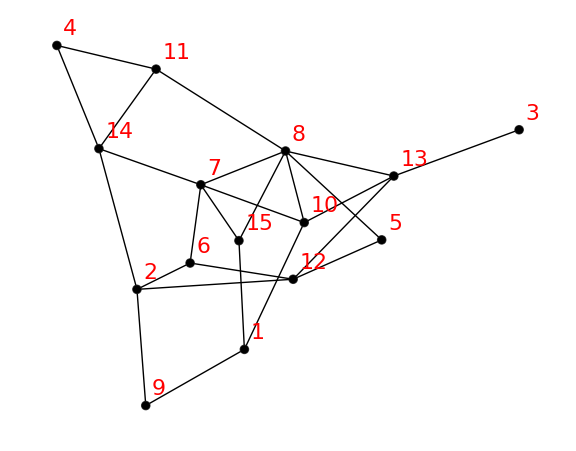

```mathematica
SeedRandom[36];

nNodes = 15;
nEdges = 25;

g = CreateRandomGraph[nNodes,nEdges];

(*nNodes = 6;
g = CompleteGraph[nNodes];*)

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];



vCoords ={{2.414338857510769,2.6730841184543714},{3.358414451242318,2.145233239104118},{0.,0.7415366790746624},{4.062126795562653,0.},{1.2075950128356883,1.7101061964597284},{2.891192663049722,2.1136638140432984-0.2},{2.7970296424741217,1.2253661678290595},{2.052741453566191,0.9284742014900683},{3.280928360962754,3.167198403825711},{1.8886237097210505,1.557870850239414},{3.190148533075726,0.2082582333304872},{1.9856923593469946,2.0562928627263695},{1.101030246956482,1.1485726665657219},{3.692477285339926,0.9075770673501602},{2.46206329310155,1.7170007179729065}};
th=Pi;
Rot = {{Cos[th],-Sin[th]},{Sin[th],Cos[th]}};
rCoords=Table[Rot.vCoords[[i,;;]],{i,1,Length[vCoords]}];

Graph[g,VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexCoordinates->rCoords,VertexLabels->"Name"]
```

```mathematica
edges[[18]]
```

7<->15

```mathematica
inputInds={{7,14},{18,11}};
```

```mathematica
(*Define the number of neurons in each layer*)
inputNeurons=2;
ns=8;
hiddenLayer1Neurons=ns;
hiddenLayer2Neurons=ns;
hiddenLayer3Neurons=ns;
outputNeurons=2;

(*Create a list of vertices for each layer*)
inputLayer=Table[Subscript["Input",i],{i,inputNeurons}];
hiddenLayer1=Table[Subscript["Hidden1",i],{i,hiddenLayer1Neurons}];
hiddenLayer2=Table[Subscript["Hidden2",i],{i,hiddenLayer2Neurons}];
hiddenLayer3=Table[Subscript["Hidden3",i],{i,hiddenLayer3Neurons}];
outputLayer=Table[Subscript["Output",i],{i,outputNeurons}];

(*Create the edges for the feedforward neural network*)
edges=Join[Flatten[Table[DirectedEdge[inputLayer[[i]],hiddenLayer1[[j]]],{i,inputNeurons},{j,hiddenLayer1Neurons}]],Flatten[Table[DirectedEdge[hiddenLayer1[[i]],hiddenLayer2[[j]]],{i,hiddenLayer1Neurons},{j,hiddenLayer2Neurons}]],(*Flatten[Table[DirectedEdge[hiddenLayer2[[i]],hiddenLayer3[[j]]],{i,hiddenLayer2Neurons},{j,hiddenLayer3Neurons}]],*)Flatten[Table[DirectedEdge[hiddenLayer2[[i]],outputLayer[[j]]],{i,hiddenLayer3Neurons},{j,outputNeurons}]]
];

(*Create the graph object*)
neuralNetworkGraph=Graph[edges];

gNet=Graph[neuralNetworkGraph,VertexStyle->Directive[Black],EdgeStyle->Directive[Black,Opacity[0.5]],ImageSize->Large];


SeedRandom[32];

nNodes = 18;
nEdges = 21;

g = CreateRandomGraph[nNodes,nEdges];

gRand=Graph[DirectedGraph[g],VertexStyle->Black,EdgeStyle->Directive[Black,Opacity[0.5]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],GraphLayout->"LayeredEmbedding"];

Grid[{{gNet},{gRand}}]
```

-Graphics-

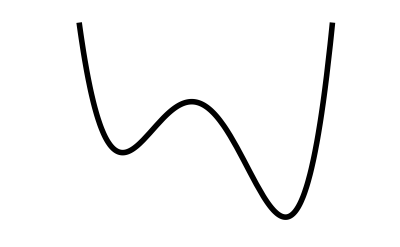

```mathematica
freeEnergyFunction[x_] := (x^2 - 1)^2 - 0.4 x

(* Plot the function *)
Plot[freeEnergyFunction[x], {x, -2, 2}, 
 PlotRange -> {-1/2,2}, Axes->False,
PlotStyle->Directive[Thickness[0.01],Black],
 Ticks -> {{-1, 0, 1}, Automatic}]
```

#### Binary Classification

```mathematica
SeedRandom[36];

nNodes = 15;
nEdges = 25;

g = CreateRandomGraph[nNodes,nEdges];

(*nNodes = 6;
g = CompleteGraph[nNodes];*)

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];



vCoords ={{2.414338857510769,2.6730841184543714},{3.358414451242318,2.145233239104118},{0.,0.7415366790746624},{4.062126795562653,0.},{1.2075950128356883,1.7101061964597284},{2.891192663049722,2.1136638140432984-0.2},{2.7970296424741217,1.2253661678290595},{2.052741453566191,0.9284742014900683},{3.280928360962754,3.167198403825711},{1.8886237097210505,1.557870850239414},{3.190148533075726,0.2082582333304872},{1.9856923593469946,2.0562928627263695},{1.101030246956482,1.1485726665657219},{3.692477285339926,0.9075770673501602},{2.46206329310155,1.7170007179729065}};
th=Pi;
Rot = {{Cos[th],-Sin[th]},{Sin[th],Cos[th]}};
rCoords=Table[Rot.vCoords[[i,;;]],{i,1,Length[vCoords]}];

Graph[g,VertexLabels->"Name",VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexCoordinates->rCoords]
```

-Graphics-

```mathematica
inputInds={{7,14},{18,11}}
```

```mathematica
inputInds
```

{{7},{18}}

```mathematica
edges[[18]]
```

7<->15

```mathematica
edges[[8]]
```

3<->13

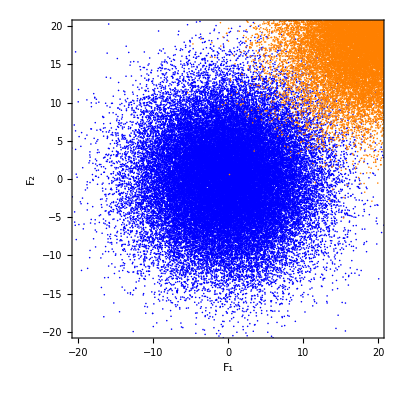

```mathematica
n=50000;  (*Sample size*)

fFac = 10;
off =1*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
μ2=1*fFac*{1,1}+fFac*off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.6;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xyList = {xy1,xy2};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)
labels = {{1,0},{0,1}};

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange]]
```

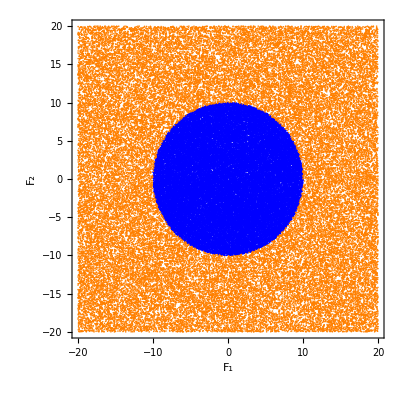

```mathematica
n = 50000;
fFac = 10;
r1 = Rectangle[{-20,-20},{20,20}]//Region;

r2 = Rectangle[{-20,-20},{0,0}]//Region;
r2a = Triangle[{{-20,-20},{0,0},{0,-20}}]//Region;
r2b= Triangle[{{-20,-20},{0,0},{-20,-10}}]//Region;
r2 =RegionUnion[r2a,r2b];
r2 =  Triangle[{{-20,-20},{20,-20},{-20,20}}]//Region;
r2 = Disk[{0,0},10]//Region;
r1= RegionDifference[r1,r2];


(*diff = RegionDifference[r2,r1];*)
xy1 = RandomPoint[r2,n];
xy2 = RandomPoint[r1,n];
xyList = {xy1,xy2};
regFrac = Area[r1]/(Area[r1]+Area[r2]);
Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange]]
```

```mathematica
edges[[18]]
```

7<->15

```mathematica
(*RandomSeed[36];*)

nIter = 1000;
timeStride = 5; 

(*numOuts = {{4},{3},{5},{9}}; (* how many output nodes - for multiclass*)*)
numOuts = {{4},{3}}; (* how many output nodes - for binary*)
inputInds={{7},{11}}; (* which input edges *)
inputInds={{7,14},{18,11}}; (* which input edges - for cirlce*)

repBool=False;
BijBool=False;
fth=5000*10^-1;

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
signs = {1,1};

deltaE=1;
deltaF=0.5;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]=-2;

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;


outsLabels = GetOutsLabels[nNodes,numOuts];

meanLists = {};
stdLists = {};


Do[
nInd = RandomInteger[Length[numOuts]-1]+1;

inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre];

outsDiffs = outsLabels[[nInd]];
{piVecNudged,fluxesNudged,frenesiesNudged}=nudgedStationaryVector[inputs,inputInds,signs,numOuts,deltaE*outsDiffs,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList,BijBool,repBool];

pisDiffs = piVecNudged -piVecPre;
EjList -= deltaF*pisDiffs;

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
FijList += deltaF*fluxesDiffs;
FijList=Clip[FijList,{-fth,fth}];

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
BijList += deltaF*fluxesDiffs;

If[Mod[iter,timeStride]==0,
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];
];

,{iter,1,nIter}];

Print["Done."]
```

Done.

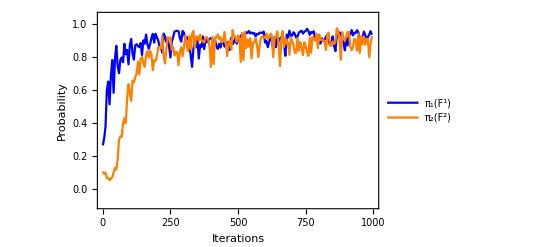

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists[[;;,1]]}];
data2 = Transpose[{iters,meanLists[[;;,2]]}];


p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,FrameLabel->{"Iterations","Probability"}],
ListPlot[data2,PlotStyle->Orange,PlotRange->Full,Joined->True]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(F^1)", "π_2(F^2)"}
]
,{0.8,0.2}]
]
```

```mathematica
fm = 1*20;
del =1*1;

m = 2;
lpd1 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[1]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd2 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[2]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
```

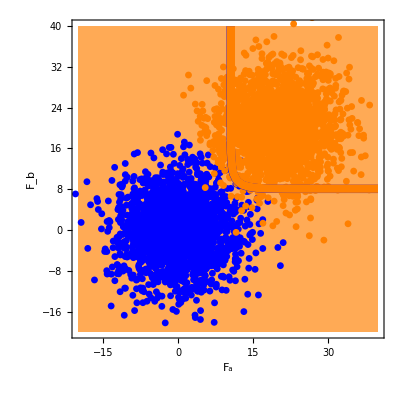

```mathematica
SetOptions[ListDensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];


lpd = lpd1;

epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[0.015],Blue]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[0.015],Orange]}},ContourShading->None][[1]];


min = 0;
max =1.0;
colf1=(Blend[{Directive[Lighter@Blue,Opacity[0.0]],Directive[Lighter@Blue,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf2=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Orange,Opacity[0.85]]},Rescale[#,{min,max}]]&);


(*colf=(ColorData[{"LakeColors",{max,min}}][#]&);*)

pD=Show[
ListDensityPlot[lpd1,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf1,(*PlotLegends->Placed[BarLegend[{colf1,{min,max}},LegendLabel->"π_1(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left],*)Epilog->{epilog1, epilog2}],

ListDensityPlot[lpd2,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf2
(*,PlotLegends->Placed[BarLegend[{colf2,{min,max}},LegendLabel->"π_2(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]*)
],

ListPlot[xy1[[1;;;;25]],PlotStyle->Directive[Blue,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy2[[1;;;;25]],PlotStyle->Directive[Orange,Opacity[1]],PlotMarkers->{Automatic,7}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/BinaryDiskSuccess.png",pD];
```

#### Schematic curving

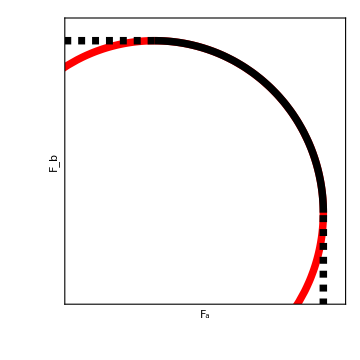

```mathematica
o = 0.8;
off = 0.5;
th = 0.015;
thf=0.0075;

p=Show[
ParametricPlot[{Cos[t]+off,Sin[t]+off},{t,-o, o+Pi/2},
AspectRatio->Automatic,
PlotStyle->Directive[Red,Thickness[th]],
PlotRange->{{0,1.6},{0,1.6}},
FrameTicks->None,
FrameStyle->Directive[Black,Thickness[thf]],
Frame->{{True,False},{True,False}},FrameLabel->{{"F_b",None},{"F_a",None}},
LabelStyle->{FontFamily->"Arial",FontSize->18},
ImageSize->Medium],

ParametricPlot[{Cos[t]+off,Sin[t]+off},{t,0, Pi/2},
AspectRatio->Automatic,
PlotStyle->Directive[Blue,Thickness[th]]],

ParametricPlot[{Cos[t]-off,1+off},{t,0, Pi/2},
AspectRatio->Automatic,
PlotStyle->Directive[Blue,Thickness[th],Dashed,Opacity[1]]],

ParametricPlot[{1+off,Sin[t] - off},{t,0, Pi/2},
AspectRatio->Automatic,
PlotStyle->Directive[Blue,Thickness[th],Dashed,Opacity[1]]]

]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/MonotonicitySchem.png",p];
```

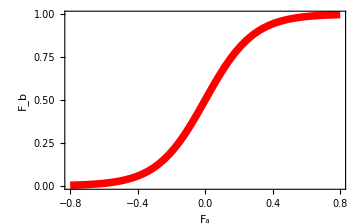

```mathematica
o = 0.8;
off = 0.5;
th = 0.015;
thf=0.0075;

p=Show[
Plot[{1-Exp[-t*7]/(1+Exp[-t*7])},{t,-o, o},
AspectRatio->Automatic,
PlotStyle->Directive[Red,Thickness[th]],
(*PlotRange->{{0,1.6},{0,1.6}},*)
FrameTicks->None,
FrameStyle->Directive[Black,Thickness[thf]],
Frame->{{True,False},{True,False}},FrameLabel->{{"F_b",None},{"F_a",None}},
LabelStyle->{FontFamily->"Arial",FontSize->18},
ImageSize->Medium]


]
```

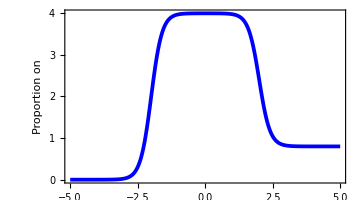

```mathematica
o = 0.8;
off = 0.5;
th = 0.0075;
thf=0.004;
sigmoid[x_]:=1/(1+Exp[-x]);
smoothBump[x_,a_,xa_,xb_]:=sigmoid[(x-xa)/a]-0.8sigmoid[(x-xb)/a];

p=Show[
Plot[4*smoothBump[t,0.2,-2,2],{t,-5, 5},
AspectRatio->Automatic,
PlotStyle->Directive[Blue,Thickness[th]],
PlotRange->Full,
FrameTicks->None,
FrameStyle->Directive[Black,Thickness[thf]],
Frame->{{True,False},{True,False}},FrameLabel->{{"Proportion on",None},{"",None}},
LabelStyle->{FontFamily->"Arial",FontSize->18},
ImageSize->Medium]

]
```

#### Turning points

```mathematica
SeedRandom[36];

nNodes = 15;
nEdges = 25;

g = CreateRandomGraph[nNodes,nEdges];

(*nNodes = 8;
g = CompleteGraph[nNodes];*)

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];



vCoords ={{2.414338857510769,2.6730841184543714},{3.358414451242318,2.145233239104118},{0.,0.7415366790746624},{4.062126795562653,0.},{1.2075950128356883,1.7101061964597284},{2.891192663049722,2.1136638140432984},{2.7970296424741217,1.2253661678290595},{2.052741453566191,0.9284742014900683},{3.280928360962754,3.167198403825711},{1.8886237097210505,1.557870850239414},{3.190148533075726,0.2082582333304872},{1.9856923593469946,2.0562928627263695},{1.101030246956482,1.1485726665657219},{3.692477285339926,0.9075770673501602},{2.46206329310155,1.7170007179729065}};
th=Pi;
Rot = {{Cos[th],-Sin[th]},{Sin[th],Cos[th]}};
rCoords=Table[Rot.vCoords[[i,;;]],{i,1,Length[vCoords]}];

Graph[DirectedGraph[g],VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red](*,VertexCoordinates->rCoords*)]
```

-Graphics-

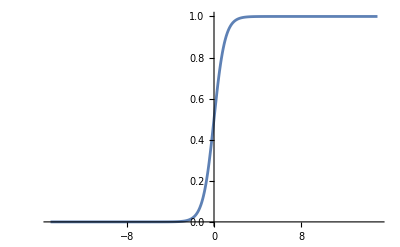

```mathematica
(*Sample size*)
sigmoid[x_]:=1/(1+Exp[-x]);
smoothBump[x_,a_,xa_,xb_]:=sigmoid[(x-xa)/a]-sigmoid[(x-xb)/a];
smoothClimb[x_,a_,xa_]:=sigmoid[(x-xa)/a];
a = 0.5;
fFac = 3;
func[F_]:=0.8(smoothBump[F,a,fFac*(-3),fFac*(-1)]+smoothBump[F,a,fFac*(1),fFac*(3)]);
as=({-3,-1,1,3,5}-1)*1;
asT = as-1;
func[F_]:=(*smoothBump[F,a,fFac*as[[1]],fFac*as[[2]]]+smoothBump[F,a,fFac*as[[3]],fFac*as[[4]]]+*)smoothClimb[F,a,fFac*as[[3]]];

fRange =fFac*3;
fRange = 15;
Plot[func[F],{F,-fRange,fRange},PlotRange->Full]
```

```mathematica
fFac*asT
```

{-12,-6,0,6,12}

```mathematica
nIter = 0;
timeStride = 5; 
(*inputInds={{7,14}}; (* which input edges - for cirlce*)
outInd = 4;*)

inputInds={{7,14}}; (* which input edges - for cirlce*)
outInd = 4;


repBool=False;
BijBool=False;


signs=ConstantArray[1,{Length[inputInds[[1]]]}];

deltaF=2;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]-=2;

(*(* M=1, inputs 7, numOuts 4*)
EjList ={0.45446372418381353,0.9393611343960351,0.38072955787395135,-2.8465173000992547,0.5365763979574453,0.6046012932836234,0.16439591294831052,0.3784329531312528,0.6244386674858143,0.35747975859023196,0.7606022051188576,0.6612242776234457,0.44516856650275544,-5.7927434039434935,0.33178625494721137};
BijList={-0.24653424219907397,-0.14280506620557226,-0.1618328226789372,-0.2842024885121397,0.09741468392164551,-0.5092610435532318,-2.4296545467237953,1.808681481889581*^-10,-1.1358994126705118,2.7805973547329255,-0.5770076010998193,-0.3799003342377293,-0.547057077914252,0.04043044958698326,0.40897556009756686,0.11145914630490411,2.499725196715315,0.08434980682222169,-0.13961974555791287,-1.7193269938442017,-0.534242612563998,-0.050223311109167314,0.002912465719255699,3.0134193881670637,-0.18171604759440035};
FijList={0.26434918989013906,-0.24278308380045632,-0.20044374071049822,0.07636748133344397,0.2855296992620042,-0.39243982404976346,0.6540332685371634,-0.38072960289059427,1.5472496216105105,-1.523080846500367,-0.615457632180884,0.5573351843140472,0.1114326812770887,-0.24425192324079883,-0.2711634285004253,-0.044021966044240496,-0.9960802475686861,-0.02042391067641245,0.5236016733214043,-1.7031229633400977,0.7313888589708369,0.488800755033508,-0.03665653908390559,-0.9955721824100314,-0.22535730912036916};*)



(* M=2, inputs 7 and 14, numOuts 4*)EjList ={-1.7520748723385497,-5.473637095340434,-3.879412785777694,-5.024712142954449,4.642831793403868,4.845135916412914,0.27808826849861723,-1.9515881789794673,-1.673024315589617,1.7318903623632478,-1.5363654837855285,-5.141805413507976,-5.0240838054134045,2.536197972936258,-0.8023387170507397};
BijList={1.7526793449187728,2.6185097008354075,-1.1308945641658807,0.001108682879179633,-1.455979669794536,-0.5153707064055678,-0.8518245531348555,-3.3825092116146713,-0.011573636409488575,-1.4832609319803287,2.840659624105998,0.4475760008937015,-5.257646726790608,2.6544899190806066,4.809846114004626,0.6362927462219131,-5.717995627220825,2.1380091075956296,-3.6638036333864488,6.232139948301541,-2.8248483904449158,-0.4384400137293972,-2.371772197592951,-4.379433577962154,-3.482995233227036};
FijList={1.812480673065745,4.583746562073281,-2.6322709979940755,0.7291104664461948,-3.958774071157163,-2.0777507636874897,-2.2750088432868747,-2.533101695941077,0.07198488601989708,2.254321241003637,-0.4605439111441866,0.520640746778895,2.5377887177107277,3.496260780387055,-1.891571087968474,1.0383565118980012,-0.4703313477977212,1.202913257075451,2.1648840272938,3.4080975559063074,-0.24229032110015888,1.631643695743564,-3.3210342055372464,1.5966909812395156,4.15603525980511};

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;

meanLists = {};

Do[
FTest = RandomReal[{-1*fRange,1fRange}];
(*FTest = fFac*RandomChoice[asT[[1;;5]]];*)
piTest = func[FTest];
inputs = {FTest};

WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList, BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre][[outInd]];
diff = piVecPre-piTest;

piPrimeE=ComputepiAndPiprimeE[inputs, inputInds,signs,g,edges,nEdges,nNodes,EjList,BijList,FijList,adjMat, BijBool,repBool];
fluxesDiffsE =piPrimeE[[outInd,;;]];

piPrimeF=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001, BijBool,repBool];
fluxesDiffsF =piPrimeF[[outInd,;;]];

piPrimeB=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001, BijBool,repBool];
fluxesDiffsB =piPrimeB[[outInd,;;]];

EjList-= deltaF*fluxesDiffsE*diff;
FijList -= deltaF*fluxesDiffsF*diff;
BijList -= deltaF*fluxesDiffsB*diff;


If[Mod[iter,timeStride]==0,
AppendTo[meanLists,diff^2];

];

,{iter,1,nIter}];

Print["Done."]
```

Done.

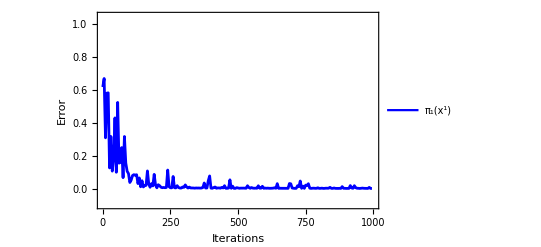

```mathematica
iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists}];


p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,FrameLabel->{"Iterations","Error"}]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(x^1)"}
]
,{0.8,0.2}]
]
```

```mathematica
EjList
```

{0.454464,0.939361,0.38073,-2.84652,0.536576,0.604601,0.164396,0.378433,0.624439,0.35748,0.760602,0.661224,0.445169,-5.79274,0.331786}

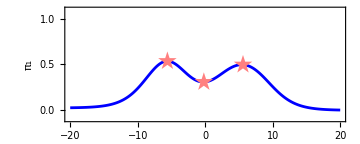

```mathematica
fm = 10;
del =0.2;

fRange = 20;
numOuts = {{4}};

signChangeCount[yValues_]:=Module[{signChanges,prevSign},signChanges=0;
prevSign=Sign[First[yValues]];
Do[If[Sign[yValues[[i]]]!=prevSign,signChanges++;
prevSign=Sign[yValues[[i]]];],{i,2,Length[yValues]}];
signChanges]

signChanges[yValues_]:=Module[{signChanges,prevSign},signChanges={};
prevSign=Sign[First[yValues]];
Do[If[Sign[yValues[[i]]]!=prevSign,AppendTo[signChanges,i];
prevSign=Sign[yValues[[i]]];],{i,2,Length[yValues]}];
signChanges]

fourthOrderDerivative[func_,x_,h_]:=(1/(12 h)) (-func[x+2 h]+8 func[x+h]-8 func[x-h]+func[x-2 h]);

ff[x_]:=MapInputOutput[{x},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList,FijList,BijBool,repBool][[1,1]];
lpdp = Table[{F1,fourthOrderDerivative[ff,F1,del]},{F1,-fRange,fRange,del}];
sc=signChanges[lpdp[[;;,2]]];


m = 1;
tf=0;
lpd = Table[{F1,Mean[MapInputOutput[{F1},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList,FijList,BijBool,repBool][[1]]]},{F1,-m*fRange,m*fRange,del}];


p=Show[
ListPlot[lpd,
PlotRange->{-0.1,1.1},Joined->True,PlotStyle->Blue,AspectRatio->2/5,(*ImageSize->Medium,*)
Frame->{{True,False},{True,False}},
FrameLabel->{{"π_1",None},{"F_a",None}},
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",FontSize->18}],

ListPlot[Table[{lpd[[sc[[i]],1]],lpd[[sc[[i]],2]]},{i,1,Length[sc]}],PlotStyle->Pink,PlotMarkers->{"★",20}]

(*Plot[func[F],{F,-fRange,fRange},PlotStyle->Directive[Blue,Opacity[1],Dashed],PlotRange->Full]*)

]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/ThreeTurningPoints.png",p];
```

#### Constraint schematic

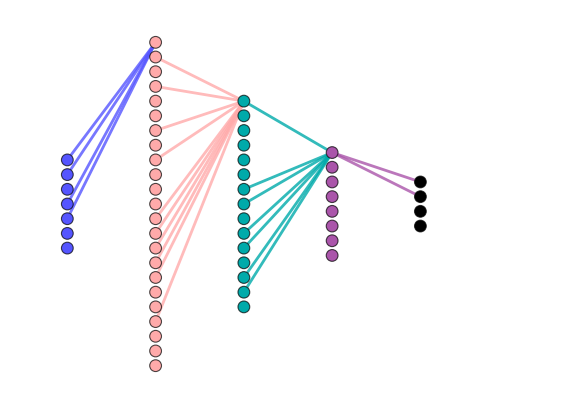

```mathematica
SeedRandom[36];

(*Define the number of neurons in each layer*)
(*nWij=9;
snWij =4;
nTreeWeights=31;
snTreeWeights = 12;
nZetas=21;
snZetas =10;
nEqcons=7;
nOutputs=5;
snOutputs = 2;*)

nWij=7;
snWij =4;
nTreeWeights=23;
snTreeWeights = 10;
nZetas=15;
snZetas =7;
nEqcons=8;
nOutputs=4;
snOutputs = 2;

(*Create a list of vertices for each layer*)
Wijs=Table[Subscript["Wij",i],{i,nWij}];
treeWeights=Table[Subscript["treeWeights",i],{i,nTreeWeights}];
zetas=Table[Subscript["zetas",i],{i,nZetas}];
eqcons=Table[Subscript["eqcons",i],{i,nEqcons}];
outputs=Table[Subscript["Output",i],{i,nOutputs}];
nodes = Join[Wijs,treeWeights,zetas,eqcons,outputs];

(*Create a list of vertices for each layer*)
horSep = 6;
verSep = 1;
WijCoords = Table[{0,verSep*(nWij/2-i+1/2)},{i,1,nWij}];
treeWeightCoords = Table[{horSep,verSep*(nTreeWeights/2-i+1/2)},{i,1,nTreeWeights}];
zetaCoords = Table[{2*horSep,verSep*(nZetas/2-i+1/2)},{i,1,nZetas}];
eqconsCoords = Table[{3*horSep,verSep*(nEqcons/2-i+1/2)},{i,1,nEqcons}];
outputCoords = Table[{4*horSep,verSep*(nOutputs/2-i+1/2)},{i,1,nOutputs}];
vCoords =Join[WijCoords,treeWeightCoords,zetaCoords,eqconsCoords,outputCoords];


(*Create the edges for the feedforward neural network*)
edges=Join[
Flatten[Table[UndirectedEdge[Wijs[[i]],treeWeights[[j]]],{i,RandomSample[Range[nWij],snWij]},{j,{1}}]],Flatten[Table[UndirectedEdge[treeWeights[[i]],zetas[[j]]],{i,RandomSample[Range[nTreeWeights],snTreeWeights]},{j,{1}}]],
Flatten[Table[UndirectedEdge[zetas[[i]],eqcons[[j]]],{i,RandomSample[Range[nZetas],snZetas]},{j,{1}}]],Flatten[Table[UndirectedEdge[eqcons[[i]],outputs[[j]]],{i,1},{j,RandomSample[Range[nOutputs],snOutputs]}]]
];

(*Create the graph object*)
neuralNetworkGraph=Graph[nodes,edges];

WijCols = Lighter@Blue;
treeWeightCols = Lighter@Pink;
zetaCols =Darker@Cyan;
eqconsCols=Lighter@Purple;
outputCols = Black;


(*Assign vertex colors*)
vertexColors=Join[
Table[WijCols,{nWij}],
Table[treeWeightCols,{nTreeWeights}],
Table[zetaCols,{nZetas}],
Table[eqconsCols,{nEqcons}],
Table[outputCols,{nOutputs}]];
vertexStyleRules=Thread[nodes->vertexColors];

eth=0.0035;
op = 0.8;
edgeColors =Join[
Table[Directive[WijCols,Thickness[eth],Opacity[op]],{snWij}],
Table[Directive[treeWeightCols,Thickness[eth],Opacity[op]],{snTreeWeights}],
Table[Directive[zetaCols,Thickness[eth],Opacity[op]],{snZetas}],
Table[Directive[eqconsCols,Thickness[eth],Opacity[op]],{snOutputs}]];
edgeStyleRules=Thread[edges->edgeColors];


gNet=Graph[neuralNetworkGraph,
VertexStyle->vertexStyleRules,
VertexSize->0.8,
EdgeStyle->edgeStyleRules,
ImageSize->Large,
ImagePadding->40,
VertexCoordinates->vCoords,PlotRange->{{-1,horSep*5 + 1},Full}]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/ConstraintNet.png",gNet,ImageResolution->300];
```

#### Multiclass Classification

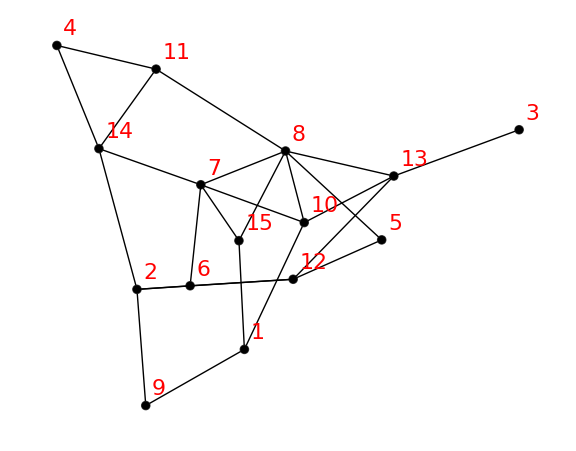

```mathematica
SeedRandom[36];

nNodes = 15;
nEdges = 25;

g = CreateRandomGraph[nNodes,nEdges];

(*nNodes = 6;
g = CompleteGraph[nNodes];*)

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];



vCoords ={{2.414338857510769,2.6730841184543714},{3.358414451242318,2.145233239104118},{0.,0.7415366790746624},{4.062126795562653,0.},{1.2075950128356883,1.7101061964597284},{2.891192663049722,2.1136638140432984},{2.7970296424741217,1.2253661678290595},{2.052741453566191,0.9284742014900683},{3.280928360962754,3.167198403825711},{1.8886237097210505,1.557870850239414},{3.190148533075726,0.2082582333304872},{1.9856923593469946,2.0562928627263695},{1.101030246956482,1.1485726665657219},{3.692477285339926,0.9075770673501602},{2.46206329310155,1.7170007179729065}};
th=Pi;
Rot = {{Cos[th],-Sin[th]},{Sin[th],Cos[th]}};
rCoords=Table[Rot.vCoords[[i,;;]],{i,1,Length[vCoords]}];

Graph[g,VertexLabels->"Name",VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexCoordinates->rCoords]
```

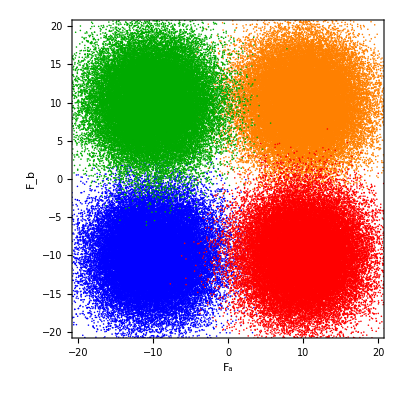

```mathematica
n=50000;  (*Sample size*)

fFac = 10;
off =0*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
(*μ2=1*fFac*{0.5,1}+fFac*off;*)
μ2=1*fFac*{1,1}+fFac*off;
μ3=1*fFac*{-1,1}+fFac*off;
μ4=1*fFac*{1,-1}+fFac*off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.4;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xy3 = RandomVariate[BinormalDistribution[μ3,{sigma,sigma},rho],n];
xy4 = RandomVariate[BinormalDistribution[μ4,{sigma,sigma},rho],n];
xyList = {xy1,xy2,xy3,xy4};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_a","F_b"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange],
ListPlot[xy3,PlotStyle->Darker@Green],
ListPlot[xy4,PlotStyle->Red]]
```

```mathematica
(*RandomSeed[36];*)

nIter = 1000;
timeStride = 10; 

numOuts = {{4},{3},{5},{9}}; (* how many output nodes - for multiclass*)
inputInds={{7},{11}}; (* which input edges *)
(*inputInds={{7,14},{18,11}}; (* which input edges - for cirlce*)*)

repBool=False;
BijBool=False;
fth=5000*10^-1;

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
signs = {1,1};

deltaE=1;
deltaF=0.5;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]=-2;

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;


outsLabels = GetOutsLabels[nNodes,numOuts];

meanLists = {};
stdLists = {};


Do[
nInd = RandomInteger[Length[numOuts]-1]+1;

inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre];

outsDiffs = outsLabels[[nInd]];
{piVecNudged,fluxesNudged,frenesiesNudged}=nudgedStationaryVector[inputs,inputInds,signs,numOuts,deltaE*outsDiffs,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList,BijBool,repBool];

pisDiffs = piVecNudged -piVecPre;
EjList -= deltaF*pisDiffs;

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
FijList += deltaF*fluxesDiffs;
FijList=Clip[FijList,{-fth,fth}];

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
BijList += deltaF*fluxesDiffs;

If[Mod[iter,timeStride]==0,
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];
];

,{iter,1,nIter}];

Print["Done."]
```

Done.

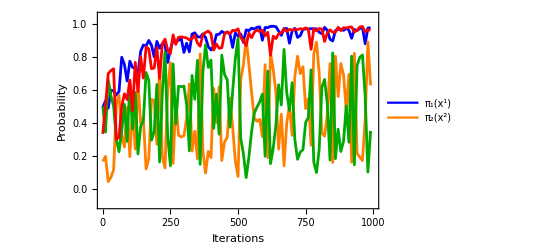

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists[[;;,1]]}];
data2 = Transpose[{iters,meanLists[[;;,2]]}];
data3 = Transpose[{iters,meanLists[[;;,3]]}];
data4 = Transpose[{iters,meanLists[[;;,4]]}];


p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,FrameLabel->{"Iterations","Probability"}],
ListPlot[data2,PlotStyle->Orange,PlotRange->Full,Joined->True],
ListPlot[data3,PlotStyle->Darker@Green,PlotRange->Full,Joined->True],
ListPlot[data4,PlotStyle->Red,PlotRange->Full,Joined->True]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(x^1)", "π_2(x^2)"}
]
,{0.8,0.2}]
]
```

```mathematica
fm = 1*20;
del =1*1;

m = 1;
lpd1 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[1]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd2 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[2]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd3 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[3]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd4 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[4]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
```

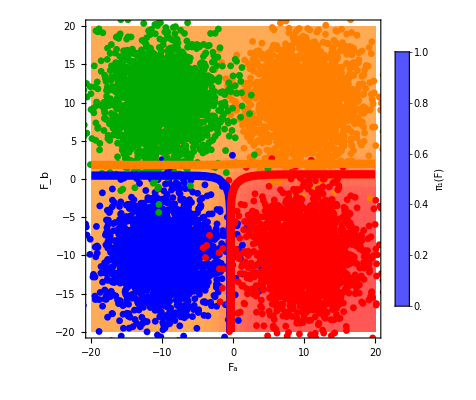

```mathematica
SetOptions[ListDensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];


epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[0.015],Blue]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[0.015],Orange]}},ContourShading->None][[1]];
epilog3=ListContourPlot[lpd3,Contours->{{0.5,Directive[Thickness[0.015],Darker@Green]}},ContourShading->None][[1]];
epilog4=ListContourPlot[lpd4,Contours->{{0.5,Directive[Thickness[0.015],Red]}},ContourShading->None][[1]];



min = 0;
max =1.0;
colf1=(Blend[{Directive[Lighter@Blue,Opacity[0.0]],Directive[Lighter@Blue,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf2=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Orange,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf3=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Green,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf4=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Red,Opacity[0.85]]},Rescale[#,{min,max}]]&);
(*colf=(ColorData[{"LakeColors",{max,min}}][#]&);*)

pD=Show[
ListDensityPlot[lpd1,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf1,PlotLegends->Placed[BarLegend[{colf1,{min,max}},LegendLabel->"π_1(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left],Epilog->{epilog1,epilog2,epilog3,epilog4}
],

ListDensityPlot[lpd2,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf2
,PlotLegends->Placed[BarLegend[{colf2,{min,max}},LegendLabel->"π_2(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListDensityPlot[lpd3,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf3
,PlotLegends->Placed[BarLegend[{colf3,{min,max}},LegendLabel->"π_3(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListDensityPlot[lpd4,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf4
,PlotLegends->Placed[BarLegend[{colf4,{min,max}},LegendLabel->"π_4(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListPlot[xy1[[1;;;;25]],PlotStyle->Directive[Blue,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy2[[1;;;;25]],PlotStyle->Directive[Orange,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy3[[1;;;;25]],PlotStyle->Directive[Darker@Green,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy4[[1;;;;25]],PlotStyle->Directive[Red,Opacity[1]],PlotMarkers->{Automatic,7}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/MultiClassFail.png",pD];
```

#### Dissipation

```mathematica
SetOptions[ListLogLinearPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

SeedRandom[36];

nNodes = 15;
nEdges = 25;

g = CreateRandomGraph[nNodes,nEdges];

(*nNodes = 6;
g = CompleteGraph[nNodes];*)

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];



vCoords ={{2.414338857510769,2.6730841184543714},{3.358414451242318,2.145233239104118},{0.,0.7415366790746624},{4.062126795562653,0.},{1.2075950128356883,1.7101061964597284},{2.891192663049722,2.1136638140432984},{2.7970296424741217,1.2253661678290595},{2.052741453566191,0.9284742014900683},{3.280928360962754,3.167198403825711},{1.8886237097210505,1.557870850239414},{3.190148533075726,0.2082582333304872},{1.9856923593469946,2.0562928627263695},{1.101030246956482,1.1485726665657219},{3.692477285339926,0.9075770673501602},{2.46206329310155,1.7170007179729065}};
th=Pi;
Rot = {{Cos[th],-Sin[th]},{Sin[th],Cos[th]}};
rCoords=Table[Rot.vCoords[[i,;;]],{i,1,Length[vCoords]}];

Graph[g,VertexLabels->"Name",VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexCoordinates->rCoords]

n=50000;  (*Sample size*)

fFac = 10;
off =1*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
μ2=1*fFac*{1,1}+fFac*off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.6;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xyList = {xy1,xy2};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)
labels = {{1,0},{0,1}};

numOuts = {{4},{3}}; (* how many output nodes - for binary*)
inputInds={{7},{11}}; (* which input edges *)

signs = {1,1};
repBool=False;
BijBool=True;
```

-Graphics-

```mathematica
(*fthList=PowerRange[0.01,10,10^(1/4)];
fthList2=PowerRange[0.01,10,10^(1/3)];
fthList=Sort[Join[fthList,fthList2]];
fthList=DeleteDuplicates[fthList,Abs[#1-#2]<10^-12&]
fthList = PrependTo[fthList,0.];*)
fthList=PowerRange[0.01,10,10^(1/5)];

accListList = {};
stdListList={};
nn=1000;

Do[
accList = {};
stdList={};
Do[
{EjList,FijList,BijList}=Import["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/Data/dissipation/trial"<>ToString[t]<>"/params_fth"<>ToString[fthList[[n]]]<>".csv","Data"];
{acc,std}=GetAccuracy[nn,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[accList,acc];
AppendTo[stdList,std];
(*Print[Max[Abs[FijList]]];*)

(*WijMat=MapInputToWijMat[{0,0},inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVec=GetStationaryVector[WijMat];
ep=GetEP[edges,nEdges,piVec,WijMat];
AppendTo[epList,ep];*)

,{n,1,Length[fthList]}];
AppendTo[accListList,accList];
AppendTo[stdListList,stdList];
,{t,1,5}];
```

```mathematica
accListList
```

{{0.497157,0.503138,0.502036,0.507867,0.533744,0.524265,0.631912,0.748405,0.847335,0.931345,0.943673,0.947456,0.959193,0.96632,0.965551,0.969795},{0.491608,0.501096,0.504369,0.500996,0.52206,0.539029,0.572835,0.786453,0.883626,0.928966,0.951273,0.954576,0.962393,0.970999,0.958308,0.967967},{0.488269,0.500374,0.493826,0.51066,0.520039,0.553379,0.575,0.755051,0.876656,0.908522,0.954349,0.947618,0.968896,0.951095,0.950743,0.960739},{0.497983,0.501694,0.504806,0.509871,0.524248,0.538064,0.620018,0.762612,0.880677,0.926511,0.951184,0.951411,0.966431,0.951567,0.963191,0.968514},{0.496577,0.492156,0.498527,0.514294,0.534745,0.570079,0.635176,0.767347,0.890093,0.926275,0.955317,0.908735,0.951917,0.970867,0.959435,0.972095}}

```mathematica
Mean[accListList]//Length
```

16

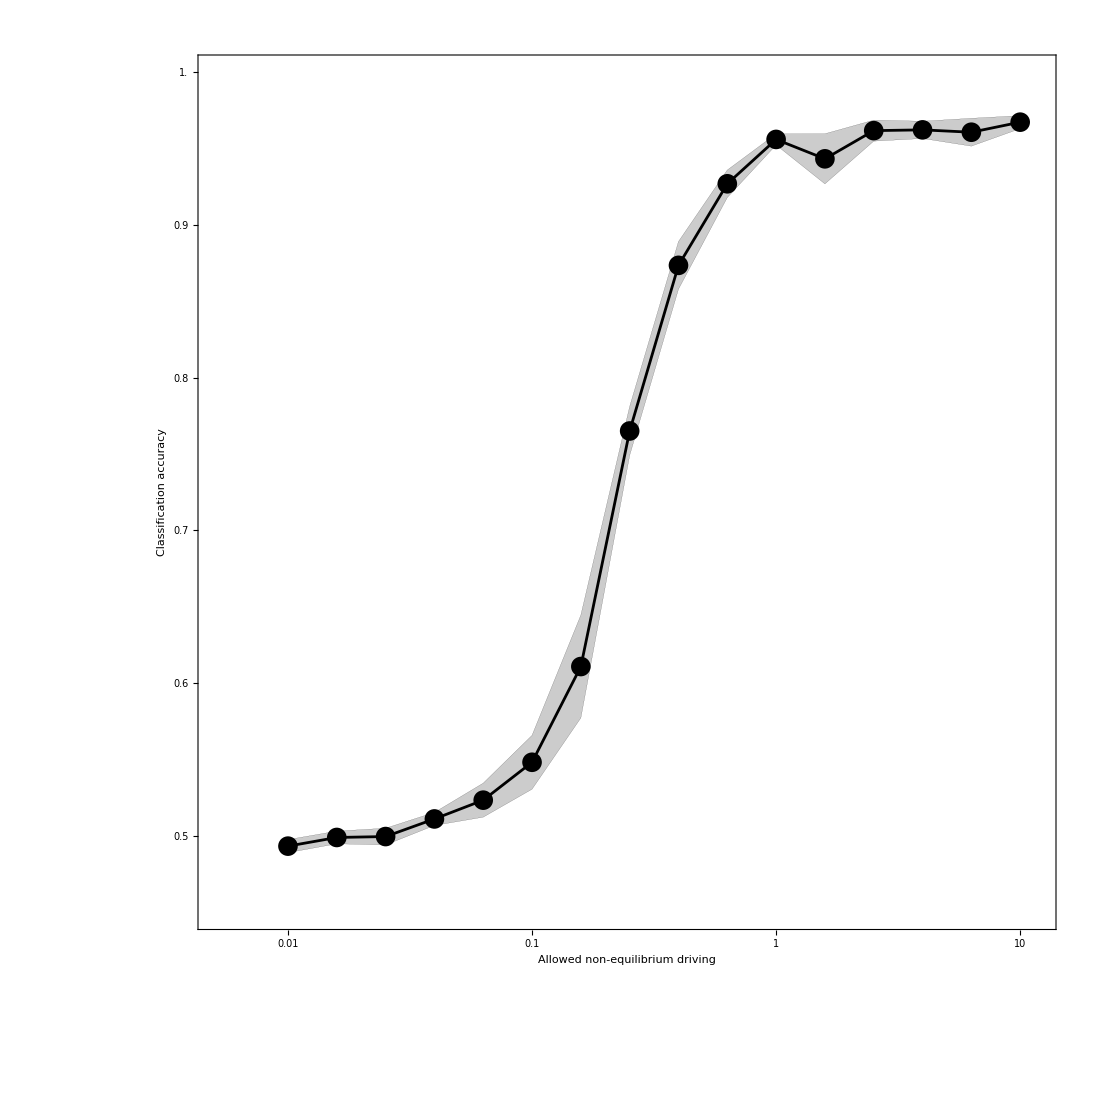

```mathematica
SetOptions[ListLogLinearPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->36}];

listData=Transpose[{fthList,Mean[accListList]}];
upData=Transpose[{fthList,Mean[accListList]+StandardDeviation[accListList]}];
downData=Transpose[{fthList,Mean[accListList]-StandardDeviation[accListList]}];
(*listData=Transpose[{fthList,accListList[[1,;;]]}];*)
p=Show[
ListLogLinearPlot[listData,AspectRatio->1,PlotRange->{{0.005,12},{0.45,1}},Joined->True,PlotStyle->Black,ImageSize->1100,FrameLabel->{(*"F_thresh"*)"Allowed non-equilibrium driving","Classification accuracy"},FrameTicks->{{{0.5,0.6,0.7,0.8,0.9,1.0},None},{{0.01,0.1,1,10},None}}],
ListLogLinearPlot[listData,PlotStyle->Black],
ListLogLinearPlot[{upData,downData},Joined->True,PlotStyle->Directive[Black,Thickness[10^-5]],Filling->{1->{2}},FillingStyle->Directive[Black,Opacity[0.2]]]

]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/NoneqDrivingBig.png",p];
```

#### Trained graph viz

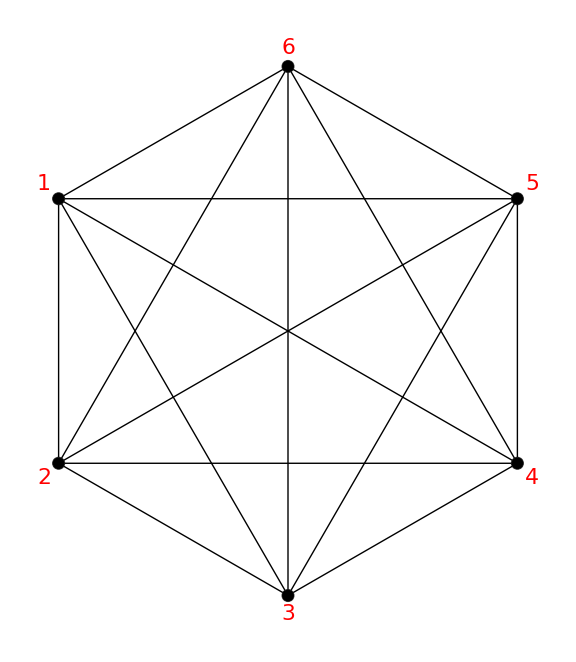

```mathematica
SeedRandom[36];

(*nNodes = 6;
g = CompleteGraph[nNodes];*)


(*nNodes = 15;
nEdges = 25;
g = CreateRandomGraph[nNodes,nEdges];
vCoords ={{2.414338857510769,2.6730841184543714},{3.358414451242318,2.145233239104118},{0.,0.7415366790746624},{4.062126795562653,0.},{1.2075950128356883,1.7101061964597284},{2.891192663049722,2.1136638140432984-0.2},{2.7970296424741217,1.2253661678290595},{2.052741453566191,0.9284742014900683},{3.280928360962754,3.167198403825711},{1.8886237097210505,1.557870850239414},{3.190148533075726,0.2082582333304872},{1.9856923593469946,2.0562928627263695},{1.101030246956482,1.1485726665657219},{3.692477285339926,0.9075770673501602},{2.46206329310155,1.7170007179729065}};
th=Pi;
Rot = {{Cos[th],-Sin[th]},{Sin[th],Cos[th]}};
rCoords=Table[i->Rot.vCoords[[i,;;]],{i,1,Length[vCoords]}];*)

nNodes = 6;
g = CompleteGraph[nNodes];
rCoords=None;


(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];


Graph[g,VertexLabels->"Name",VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexCoordinates->rCoords]
coords = GraphEmbedding[g];
vcoords = Table[i->coords[[i]],{i,1,Length[coords]}];
```

```mathematica
rCoords
```

{1→{-2.41434,-2.67308},2→{-3.35841,-2.14523},3→{0.,-0.741537},4→{-4.06213,0.},5→{-1.2076,-1.71011},6→{-2.89119,-1.91366},7→{-2.79703,-1.22537},8→{-2.05274,-0.928474},9→{-3.28093,-3.1672},10→{-1.88862,-1.55787},11→{-3.19015,-0.208258},12→{-1.98569,-2.05629},13→{-1.10103,-1.14857},14→{-3.69248,-0.907577},15→{-2.46206,-1.717}}

```mathematica
Graph
```

{{-0.866025,0.5},{-0.866025,-0.5},{3.82857×10^-16,-1.},{0.866025,-0.5},{0.866025,0.5},{1.83697×10^-16,1.}}

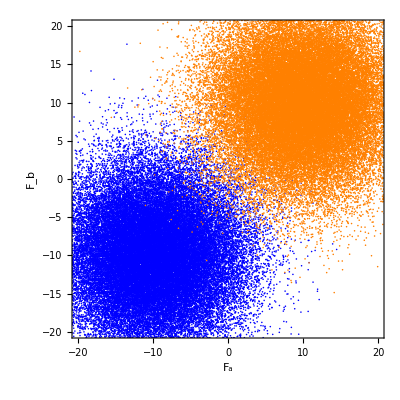

```mathematica
n=50000;  (*Sample size*)

fFac = 10;
off =0*{1,1};
μ1 =1*fFac*{-1,1} +fFac*off;
μ2=1*fFac*{1,-1}+fFac*off;

μ1 =1*fFac*{-1,-1} +fFac*off;
μ2=1*fFac*{1,1}+fFac*off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.6;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xyList = {xy1,xy2};
labels = {{1,0},{0,1}};

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_a","F_b"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange]]
```

```mathematica
(*RandomSeed[36];*)
RandomSeed[18];

nIter = 1000;
timeStride = 5; 

numOuts = {{1},{2}}; (* how many output nodes - for binary*)
inputInds={{10},{15}}; (* which input edges *)

(*numOuts = {{4},{3}}; (* how many output nodes - for binary*)
inputInds={{7},{11}}; (* which input edges *)*)

repBool=False;
BijBool=False;
fth=5000*10^-1;

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
signs = {1,1};

deltaE=0.5;
deltaF=0.5;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]=-2;

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;


outsLabels = GetOutsLabels[nNodes,numOuts];

meanLists = {};
stdLists = {};


Do[
nInd = RandomInteger[Length[numOuts]-1]+1;

inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre];

outsDiffs = outsLabels[[nInd]];
{piVecNudged,fluxesNudged,frenesiesNudged}=nudgedStationaryVector[inputs,inputInds,signs,numOuts,deltaE*outsDiffs,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList,BijBool,repBool];

pisDiffs = piVecNudged -piVecPre;
EjList -= deltaF*pisDiffs;

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
FijList += deltaF*fluxesDiffs;
(*FijList=Clip[FijList,{-fth,fth}];*)

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
BijList += deltaF*fluxesDiffs;

If[Mod[iter,timeStride]==0,
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];
];

,{iter,1,nIter}];

Print["Done."]
```

Done.

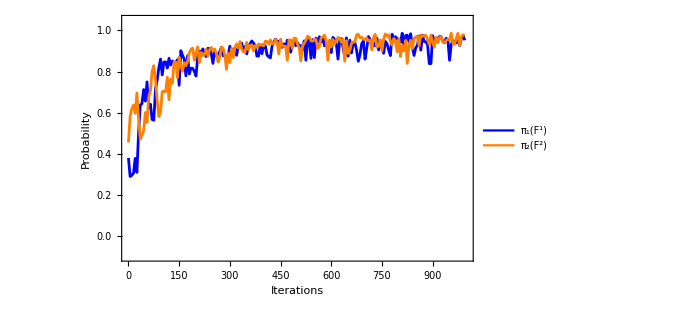

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists[[;;,1]]}];
data2 = Transpose[{iters,meanLists[[;;,2]]}];


p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,ImageSize->500,FrameLabel->{"Iterations","Probability"}],
ListPlot[data2,PlotStyle->Orange,PlotRange->Full,Joined->True]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(F^1)", "π_2(F^2)"},
LabelStyle->{FontFamily->"Arial",FontSize->20}
]
,{0.8,0.25}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/HexConvergence.png",p];
(*Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/RandomConvergence.png",p];*)
```

```mathematica
fm = 1*20;
del =1*1;

m = 1;
lpd1 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[1]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd2 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[2]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
```

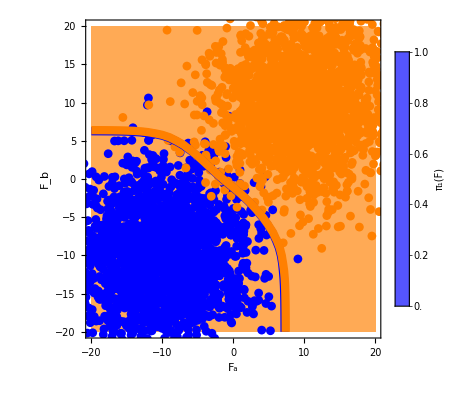

```mathematica
SetOptions[ListDensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];


lpd = lpd1;

epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[0.015],Blend[{Blue,Black},0.0]]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[0.015],Blend[{Orange,Black},0.0]]}},ContourShading->None][[1]];


min = 0;
max =1.0;
colf1=(Blend[{Directive[Lighter@Blue,Opacity[0.0]],Directive[Lighter@Blue,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf2=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Orange,Opacity[0.85]]},Rescale[#,{min,max}]]&);


(*colf=(ColorData[{"LakeColors",{max,min}}][#]&);*)

pD=Show[
ListDensityPlot[lpd1,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf1,PlotLegends->Placed[BarLegend[{colf1,{min,max}},LegendLabel->"π_1(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left],Epilog->{epilog1, epilog2}],

ListDensityPlot[lpd2,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf2
,PlotLegends->Placed[BarLegend[{colf2,{min,max}},LegendLabel->"π_2(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListPlot[xy1[[1;;;;25]],PlotStyle->Directive[Blue,Opacity[1]],PlotMarkers->{Automatic,9}],

ListPlot[xy2[[1;;;;25]],PlotStyle->Directive[Orange,Opacity[1]],PlotMarkers->{Automatic,9}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/HexClassification.png",pD];
(*Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/RandomClassification.png",pD];*)
```

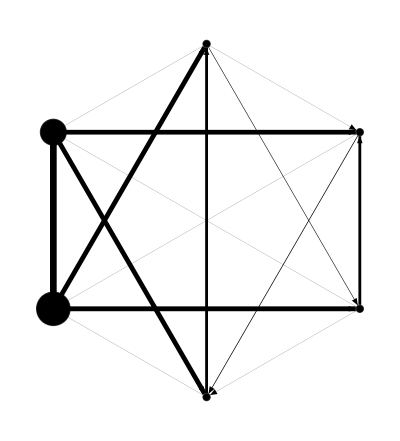

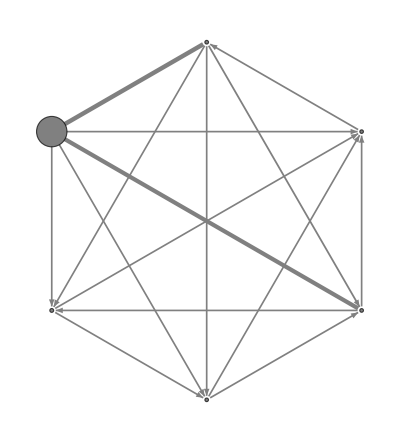

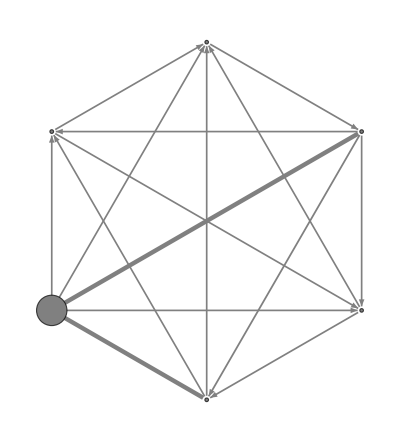

```mathematica
scFac = 0.01;
arFac=0.08;
pFac = 0.15;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.04;
edgeMin = 0.002;

pG1=DrawParamGraph[0*μ1,inputInds,signs,paramBool,numOuts,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList, scFac,arFac,arMin,edgeMin,pMin,pFac,nodeCol,edgeCol,None,False]


scFac = 0.005;
arFac=0.12;
pFac = 0.15;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.02;
edgeMin = 0.003;

nodeCol = {Gray,Gray};
edgeCol = Gray;

pF1=DrawFluxGraph[μ1,inputInds,signs,paramBool,numOuts,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList, scFac,arFac,arMin,edgeMin,pMin,pFac,nodeCol,edgeCol,None,False]

pF2=DrawFluxGraph[μ2,inputInds,signs,paramBool,numOuts,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList, scFac,arFac,arMin,edgeMin,pMin,pFac,nodeCol,edgeCol,None,False]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/HexInput1.png",pF1,ImageResolution->300];
(*Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/HexParam.png",pG1,ImageResolution->300];*)
```

```mathematica
arFac*FijList/Max[Abs[FijList]]
```

{-0.00203507,-0.031923,0.0772972,-0.0330842,0.08,0.0699198,-0.0292743,0.071062,-0.0285446,-0.00676215,-0.000667611,0.00190171,-0.00182395,-0.00152823,-0.00541887}

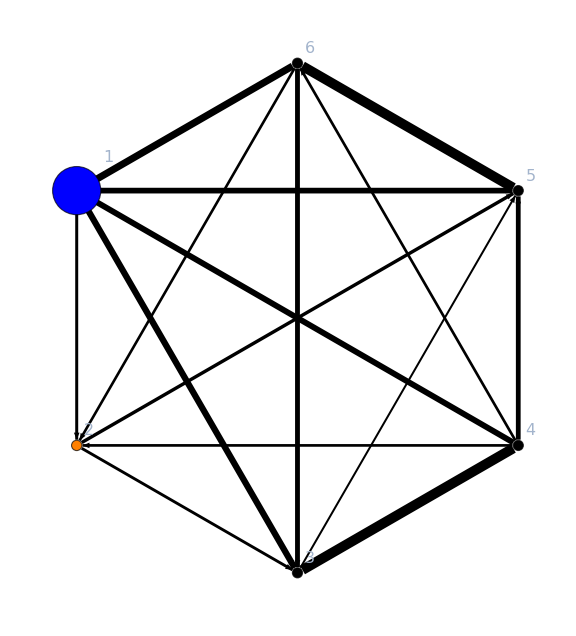

```mathematica
scFac = 0.01;
arFac=0.1;
pFac = 0.15;
paramBool = False;
nodeCol = {Blue,Orange};
edgeCol = Black;
arMin = 0.04;
pMin = 0.04;
edgeMin = 0.0025;

pG1=DrawInputOutputGraph[μ1,inputInds,signs,paramBool,numOuts,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList, scFac,arFac,arMin,edgeMin,pMin,pFac,nodeCol,edgeCol,coords,False]
```

```mathematica
edges[[15]]
```

5<->6

```mathematica
(*Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/BinaryDiskSuccess.png",pD];*)
```

#### Low dimensionality

```mathematica
SeedRandom[38];

nNodes = 6;
nEdges = 15;
(*
g = CreateRandomGraph[nNodes,nEdges];*)

nNodes = 6;
g = CompleteGraph[nNodes];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];


Graph[g,VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexLabels->"Name"]
```

-Graphics-

```mathematica
trees = GetSpanningTrees[g,nNodes];
Length[trees]
```

1296

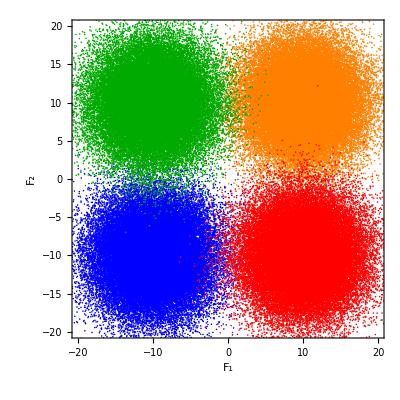

```mathematica
n=50000;  (*Sample size*)

fFac = 10;
off =0*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
(*μ2=1*fFac*{0.5,1}+fFac*off;*)
μ2=1*fFac*{1,1}+fFac*off;
μ3=1*fFac*{-1,1}+fFac*off;
μ4=1*fFac*{1,-1}+fFac*off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.4;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xy3 = RandomVariate[BinormalDistribution[μ3,{sigma,sigma},rho],n];
xy4 = RandomVariate[BinormalDistribution[μ4,{sigma,sigma},rho],n];
xyList = {xy1,xy2,xy3,xy4};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange],
ListPlot[xy3,PlotStyle->Darker@Green],
ListPlot[xy4,PlotStyle->Red]]
```

```mathematica
RandomSeed[36];

nIter = 2000;
timeStride = 10; 

numOuts = {{6},{4},{3},{5}}; (* how many output nodes - for multiclass*)
(*inputInds={{7},{11}}; (* which input edges *)*)
inputInds={{5,14},{15,11}}; (* which input edges - for cirlce*)

(*numOuts = {{6},{4}}; (* how many output nodes - for multiclass*)
(*inputInds={{7},{11}}; (* which input edges *)*)
inputInds={{5,14},{15,11}}; (* which input edges - for cirlce*)*)

repBool=False;
BijBool=False;
fth=5000*10^-1;

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
signs = {1,1};

deltaE=1;
deltaF=0.5;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]=-0;

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;


outsLabels = GetOutsLabels[nNodes,numOuts];

meanLists = {};
stdLists = {};


Do[
nInd = RandomInteger[Length[numOuts]-1]+1;

inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre];

outsDiffs = outsLabels[[nInd]];
{piVecNudged,fluxesNudged,frenesiesNudged}=nudgedStationaryVector[inputs,inputInds,signs,numOuts,deltaE*outsDiffs,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList,BijBool,repBool];

pisDiffs = piVecNudged -piVecPre;
EjList -= deltaF*pisDiffs;

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
FijList += deltaF*fluxesDiffs;
FijList=Clip[FijList,{-fth,fth}];

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
BijList += deltaF*fluxesDiffs;

If[Mod[iter,timeStride]==0,
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];
];

,{iter,1,nIter}];

Print["Done."]
```

Done.

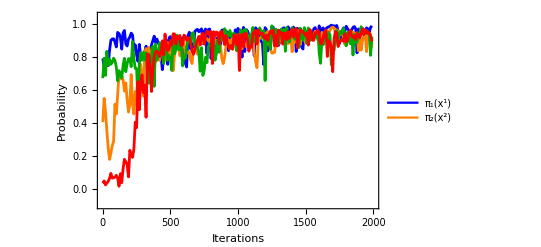

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists[[;;,1]]}];
data2 = Transpose[{iters,meanLists[[;;,2]]}];
data3 = Transpose[{iters,meanLists[[;;,3]]}];
data4 = Transpose[{iters,meanLists[[;;,4]]}];


p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,FrameLabel->{"Iterations","Probability"}],
ListPlot[data2,PlotStyle->Orange,PlotRange->Full,Joined->True],
ListPlot[data3,PlotStyle->Darker@Green,PlotRange->Full,Joined->True],
ListPlot[data4,PlotStyle->Red,PlotRange->Full,Joined->True]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(x^1)", "π_2(x^2)"}
]
,{0.8,0.2}]
]
```

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];
```

```mathematica
histEls={};

inputs = μ4;

prListUList ={};
prListList={};

a = 0.0;
aList ={};

Do[
prListU={};
prList={};
Do[

EjListt=EjListInit ;
BijListt=BijListInit;
FijListt=FijListInit;
WijMat = MapInputToWijMat[a*inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool];
histEls={};
Do[
oTree = OrientTree[trees[[m]],numOuts[[k,1]]];
AppendTo[histEls,TreeWeight[oTree,WijMat]]
,{m,1,Length[trees]}];
pr=(Total[histEls]^2/Total[histEls^2])/(Length[trees]);
AppendTo[prListU,pr];

EjListt=EjList;
BijListt=BijList;
FijListt=FijList;
WijMat = MapInputToWijMat[a*inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool];
histEls={};
Do[
oTree = OrientTree[trees[[m]],numOuts[[k,1]]];
AppendTo[histEls,TreeWeight[oTree,WijMat]]
,{m,1,Length[trees]}];
pr=(Total[histEls]^2/Total[histEls^2])/(Length[trees]);
AppendTo[prList,pr];


,{k,1,4}];

AppendTo[prListUList,prListU];
AppendTo[prListList,prList];
AppendTo[aList,a];
,{a,0,1,.1}];
```

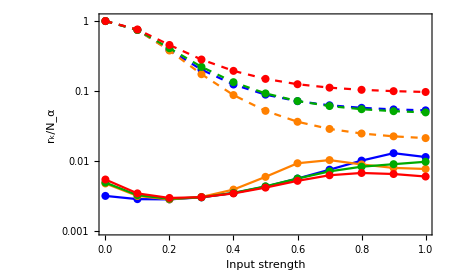

```mathematica
SetOptions[ListLogPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

lp=ListLogPlot;

cols = {Blue,Orange,Darker@Green,Red};

pList={};

Do[
data=Transpose[{aList,Transpose[prListList][[k]]}];
dataU=Transpose[{aList,Transpose[prListUList][[k]]}];
AppendTo[pList,
Show[
lp[data,PlotStyle->Directive[cols[[k]]],PlotRange->{0.001,1.1},Joined->True,
FrameLabel->{"Input strength", "r_k/N_α"},ImageSize->450],
lp[data,PlotStyle->Directive[cols[[k]]]],
lp[dataU,Joined->True,PlotStyle->Directive[cols[[k]],Dashed]],
lp[dataU,PlotStyle->Directive[cols[[k]]]]
]
];

,{k,1,4}];



(* p=Show[Legended[pList,
Placed[LineLegend[{Directive[Blue],Directive[Blue,Dashed]},{"Trained","Untrained"},LabelStyle->{FontFamily->"Arial",FontSize->18}],{0.76,0.8}]]]*)

p=Show[pList]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/DimensionalityPlotsP4.png",p];
```

```mathematica
GetTreeFrenesy[tree_,frenesies_]:=Module[
{weight, edge},
weight = 0;
Do[
edge = tree[[i]];
weight += frenesies[[Position[edges,edge][[1,1]]]];
,{i,1,Length[tree]}];
weight
]


EjListt=EjListInit ;
BijListt=BijListInit;
FijListt=FijListInit;

(*EjListt=EjList;
BijListt=BijList;
FijListt=FijList;*)


WijMat=MapInputToWijMat[0*inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool];
piVec = GetStationaryVector[WijMat];
frenesies = GetEdgeFrenesies[edges,nEdges,piVec,WijMat];
```

```mathematica
EjListt=EjListInit ;
BijListt=BijListInit;
FijListt=FijListInit;

(*EjListt=EjList;
BijListt=BijList;
FijListt=FijList;*)


tfs=GetTreeFrenesy[#,frenesies]&/@trees;

tfArray = {};
fm = 20;
m = 1;
del = 1;
distances = {};
μList = {μ1,μ2,μ3,μ4};
Do[
subdist={};
Do[
inputs = xyList[[μind]][[iter]];
WijMat=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool];
piVec = GetStationaryVector[WijMat];
frenesies = GetEdgeFrenesies[edges,nEdges,piVec,WijMat];
tfs=GetTreeFrenesy[#,frenesies]&/@trees;

(*distance = N[Norm[{F1,F2}-#]&/@{μ1,μ2,μ3,μ4}];*)
distance = Norm[inputs-μList[[μind]]];
AppendTo[subdist,distance];

AppendTo[tfArray,tfs->μind];
,{iter,1,200}];
AppendTo[distances,subdist];
,{μind,{1,2,3,4}}];
```

```mathematica
tfArrayInit = tfArray
```

```mathematica
tfArrayFin = tfArray
```

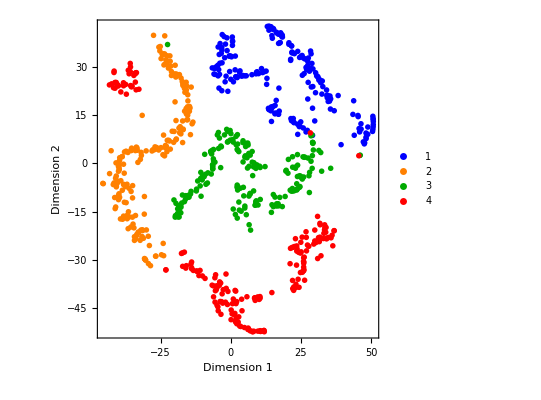

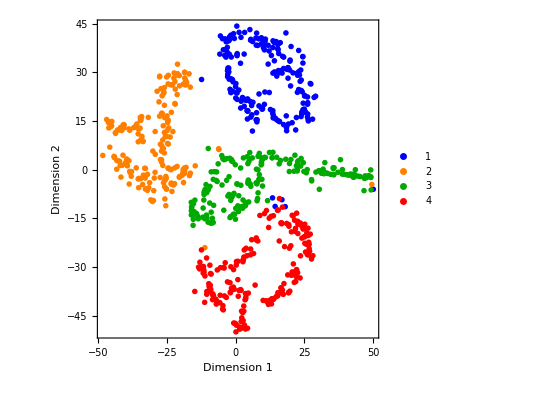

```mathematica
(*reducedInit= DimensionReduction[tfArrayInit[[All,1]],2,Method->{"TSNE","Perplexity"->40}];
reducedFin= DimensionReduction[tfArrayFin[[All,1]],2,Method->{"TSNE","Perplexity"->40}];*)

reducedInit= DimensionReduction[tfArrayInit[[All,1]],2,Method->{"TSNE","Perplexity"->10}];
reducedFin= DimensionReduction[tfArrayFin[[All,1]],2,Method->{"TSNE","Perplexity"->10}];

featuresInit=GroupBy[tfArrayInit,Last->First];
reducedfeaturesInit=reducedInit/@featuresInit;
pl=ListPlot[Values[reducedfeaturesInit],PlotLegends->Keys[reducedfeaturesInit],
PlotMarkers->{●,Medium},PlotStyle->{Blue,Orange,Darker@Green,Red},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"}]

featuresFin=GroupBy[tfArrayFin,Last->First];
reducedfeaturesFin=reducedFin/@featuresFin;
pl=ListPlot[Values[reducedfeaturesFin],PlotLegends->Keys[reducedfeaturesFin],
PlotMarkers->{●,Medium},PlotStyle->{Blue,Orange,Darker@Green,Red},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"}]
```

```mathematica
features=GroupBy[tfArray,Last->First];
reducedfeatures=reduced/@features;
ListPointPlot3D[Values[reducedfeatures]]
```

-Graphics3D-

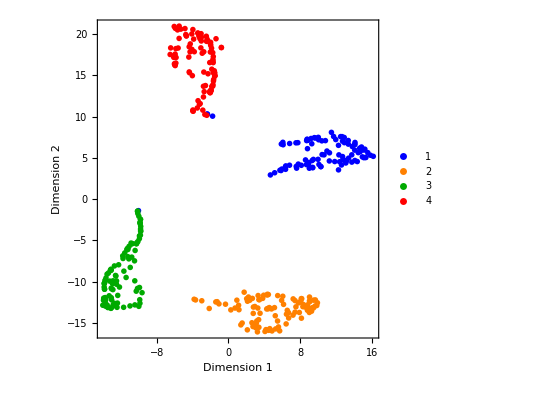

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

features=GroupBy[tfArray,Last->First];
reducedfeatures=reduced/@features;
pl=ListPlot[Values[reducedfeatures],PlotLegends->Keys[reducedfeatures],
PlotMarkers->{●,Medium},PlotStyle->{Blue,Orange,Darker@Green,Red},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"}]
```

```mathematica
pl=ListPlot[Values[reducedfeatures],PlotLegends->Keys[reducedfeatures],
PlotMarkers->{●},PlotStyle->{Table[Directive[Blue,AbsolutePointSize[10]],{i,1,100}],Orange,Darker@Green,Red},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"}]
```

-Graphics-

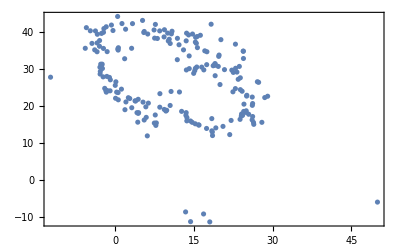

```mathematica
ListPlot[Values[reducedfeaturesFin][[1]]]
```

```mathematica
sInitList = {};
sFinList = {};
Do[

reducedInit= DimensionReduction[tfArrayInit[[All,1]],2,Method->{"TSNE","Perplexity"->p}];
reducedFin= DimensionReduction[tfArrayFin[[All,1]],2,Method->{"TSNE","Perplexity"->p}];

reducedfeaturesInit=reducedInit/@featuresInit;
reducedfeaturesFin=reducedFin/@featuresFin;

sInit=ClusteringMeasurements[reducedfeaturesInit,"Silhouette"];
sFin=ClusteringMeasurements[reducedfeaturesFin,"Silhouette"];

AppendTo[sInitList,sInit];
AppendTo[sFinList, sFin];

,{p,Join[{1},Range[5,50,5]]}]
```

```mathematica
Join[{1},Range[5,50,5]]
```

{1,5,10,15,20,25,30,35,40,45,50}

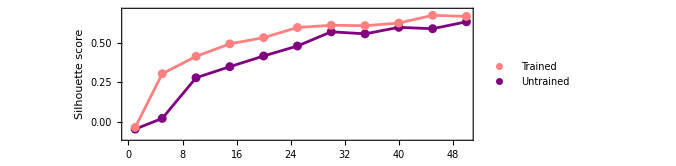

```mathematica
datInit = Transpose[{Join[{1},Range[5,50,5]],sInitList}];
datFin = Transpose[{Join[{1},Range[5,50,5]],sFinList}];
c1 = Purple;
c2 = Pink;
pl=Legended[
Show[
ListPlot[datInit,PlotStyle->c1,PlotRange->{-0.1,0.7},FrameLabel->{"Perplexity","Silhouette score"},AspectRatio->1/3,ImageSize->500],
ListPlot[datInit,PlotStyle->c1,Joined->True,PlotRange->Full],
ListPlot[datFin,PlotStyle->c2,PlotRange->Full],
ListPlot[datFin,PlotStyle->c2,Joined->True,PlotRange->Full]]
,
Placed[
PointLegend[{c2,c1},{"Trained","Untrained"},LabelStyle->{FontFamily->"Arial",FontSize->18}
]
,{0.8,0.25}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/PerplexityPlot.png",pl,ImageResolution->300];
```

```mathematica
Keys[reducedfeatures]
```

{1,2,3,4}

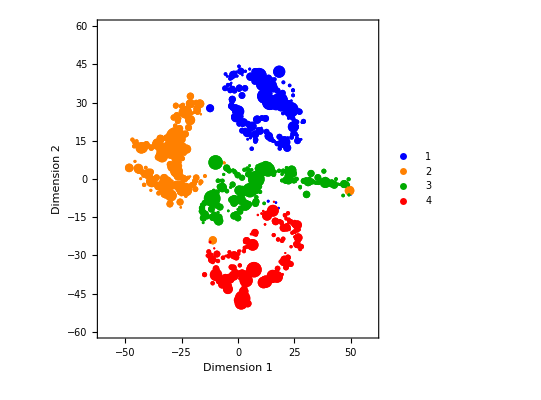

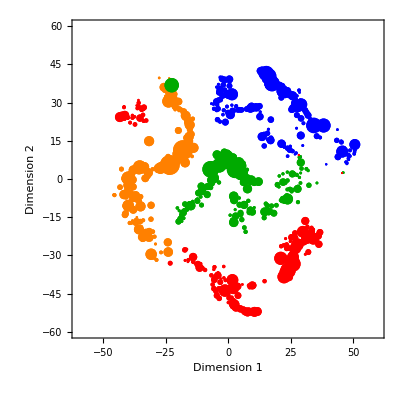

```mathematica
colors = {Blue,Orange,Darker@Green,Red};
plFin=Legended[

Show[Table[
ListPlot[Transpose[{Values[reducedfeaturesFin][[k]]}],PlotRange->3*{{-20,20},{-20,20}},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"},PlotStyle->Table[Directive[colors[[k]],●,PointSize[0.05*1/(distances[[k]][[i]]+1)]],{i,1,100}]],{k ,1,4}]
]
,
Placed[
PointLegend[colors,{"1","2","3","4"},LabelStyle->{FontFamily->"Arial",FontSize->18}
]
,{0.85,0.75}]

]


(*plInit=Legended[

Show[Table[
ListPlot[Transpose[{Values[reducedfeaturesInit][[k]]}],PlotRange->3*{{-20,20},{-20,20}},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"},PlotStyle->Table[Directive[colors[[k]],●,PointSize[0.05*1/(distances[[k]][[i]]+1)]],{i,1,100}]],{k ,1,4}]
]
,
Placed[
PointLegend[colors,{"1","2","3","4"},LabelStyle->{FontFamily->"Arial",FontSize->18}
]
,{0.85,0.75}]

]*)

plInit=Show[Table[
ListPlot[Transpose[{Values[reducedfeaturesInit][[k]]}],PlotRange->3*{{-20,20},{-20,20}},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"},PlotStyle->Table[Directive[colors[[k]],●,PointSize[0.05*1/(distances[[k]][[i]]+1)]],{i,1,100}]],{k ,1,4}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TSNEInit.png",plInit,ImageResolution->300];
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TSNEFin.png",plFin,ImageResolution->300];
```

```mathematica
fm = 1*20;
del =1*1;

m = 1;
lpd1 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[1]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd2 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[2]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd3 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[3]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd4 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[4]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
```

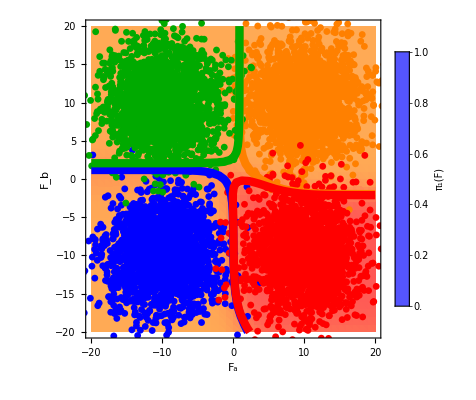

```mathematica
SetOptions[ListDensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];


epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[0.015],Blue]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[0.015],Orange]}},ContourShading->None][[1]];
epilog3=ListContourPlot[lpd3,Contours->{{0.5,Directive[Thickness[0.015],Darker@Green]}},ContourShading->None][[1]];
epilog4=ListContourPlot[lpd4,Contours->{{0.5,Directive[Thickness[0.015],Red]}},ContourShading->None][[1]];



min = 0;
max =1.0;
colf1=(Blend[{Directive[Lighter@Blue,Opacity[0.0]],Directive[Lighter@Blue,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf2=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Orange,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf3=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Green,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf4=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Red,Opacity[0.85]]},Rescale[#,{min,max}]]&);
(*colf=(ColorData[{"LakeColors",{max,min}}][#]&);*)

pD=Show[
ListDensityPlot[lpd1,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf1,PlotLegends->Placed[BarLegend[{colf1,{min,max}},LegendLabel->"π_1(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left],Epilog->{epilog1,epilog2,epilog3,epilog4}
],

ListDensityPlot[lpd2,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf2
,PlotLegends->Placed[BarLegend[{colf2,{min,max}},LegendLabel->"π_2(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListDensityPlot[lpd3,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf3
,PlotLegends->Placed[BarLegend[{colf3,{min,max}},LegendLabel->"π_3(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListDensityPlot[lpd4,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf4
,PlotLegends->Placed[BarLegend[{colf4,{min,max}},LegendLabel->"π_4(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListPlot[xy1[[1;;;;25]],PlotStyle->Directive[Blue,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy2[[1;;;;25]],PlotStyle->Directive[Orange,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy3[[1;;;;25]],PlotStyle->Directive[Darker@Green,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy4[[1;;;;25]],PlotStyle->Directive[Red,Opacity[1]],PlotMarkers->{Automatic,7}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/HexGraphFourClassClassification.png",pD];
```

-5.65123

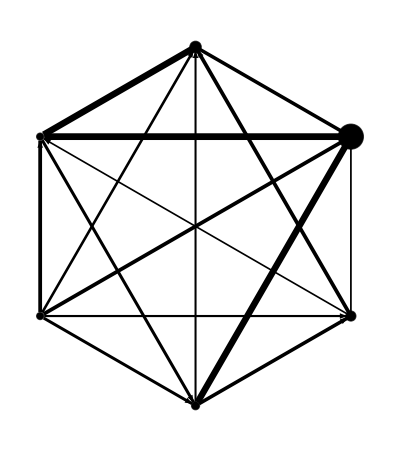

```mathematica
(*scFac = 0.005;
arFac=0.12;
pFac = 0.15;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.02;
edgeMin = 0.003;*)

scFac = 0.001;
arFac=0.08;
pFac = 0.1;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.04;
edgeMin = 0.003;

pG1=DrawParamGraph[0*μ1,inputInds,signs,paramBool,numOuts,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList, scFac,arFac,arMin,edgeMin,pMin,pFac,nodeCol,edgeCol,{},False]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TrainedGraphHexFourClassParams.png",pG1];
```

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];
```

```mathematica
numOuts
```

{{6},{4},{3},{5}}

```mathematica
ind =numOuts[[1,1]];
Psi1=GetPsiVec[6,trees,EjList,BijList,FijList,uiαArray];
Psi2=GetPsiVec[4,trees,EjList,BijList,FijList,uiαArray];
Psi3=GetPsiVec[3,trees,EjList,BijList,FijList,uiαArray];
Psi4=GetPsiVec[5,trees,EjList,BijList,FijList,uiαArray];

PsiArray={Psi1,Psi2,Psi3,Psi4};

inputs = μ3;
Chi1=GetChiVec[6,trees,inputs,viαArray];
Chi2=GetChiVec[4,trees,inputs,viαArray];
Chi3=GetChiVec[3,trees,inputs,viαArray];
Chi4=GetChiVec[5,trees,inputs,viαArray];
ChiArray={Chi1,Chi2,Chi3,Chi4};
```

```mathematica
dotArray = ConstantArray[0,{4,4}];
inputsList = {μ1,μ2,μ3,μ4};
Do[
inputs=inputsList[[ci]];
Chi1=GetChiVec[6,trees,inputs,viαArray];
Chi2=GetChiVec[4,trees,inputs,viαArray];
Chi3=GetChiVec[3,trees,inputs,viαArray];
Chi4=GetChiVec[5,trees,inputs,viαArray];
ChiArray={Chi1,Chi2,Chi3,Chi4};
Do[
(*dotArray[[pi,ci]]=PsiArray[[pi]].ChiArray[[pi]];*)
dotArray[[pi,ci]]=Normalize[PsiArray[[pi]]].ChiArray[[pi]]
,{pi,1,4}],{ci,1,4}]
```

```mathematica
dotArray//MatrixForm
```

(5.10106×10^8 | 0.00085896 | 78957. | 66.3575
23905.5 | 470.548 | 507542. | 60634.9
6852.19 | 593.889 | 5.09468×10^8 | 31.7332
39118. | 0.118067 | 263752. | 527.567)

```mathematica
Map[Norm,PsiArray]//Normalize
```

{0.430989,0.900506,0.0529587,0.0230682}

```mathematica
Norm[ChiArray[[1]]]//N
```

1.38721×10^7

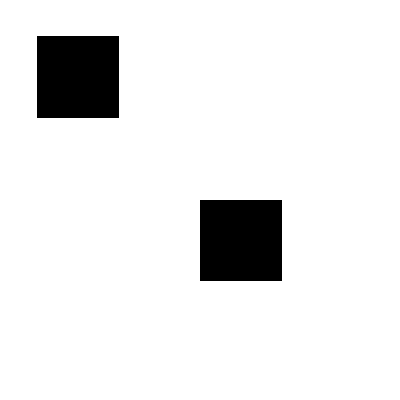

```mathematica
ArrayPlot[dotArray]
```

```mathematica
Norm[Psi1]
```

9.3456×10^7

```mathematica
Norm[Psi3]
```

3.885×10^7

```mathematica
Psi1.Psi4
```

0.951844

#### Low dimensionality random

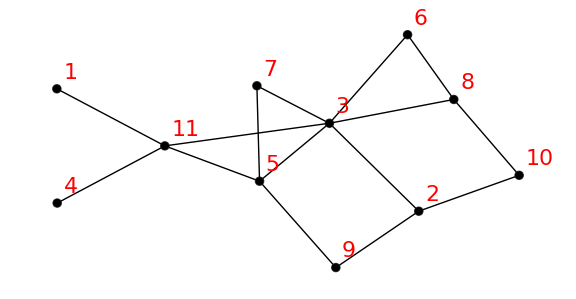

```mathematica
SeedRandom[34];

nNodes = 11;
nEdges = 15;

g = CreateRandomGraph[nNodes,nEdges];


(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];


Graph[g,VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexLabels->"Name"]
```

```mathematica
trees = GetSpanningTrees[g,nNodes];
```

```mathematica
Length[trees]
```

284

```mathematica
n=50000;  (*Sample size*)

fFac = 10;
off =0*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
(*μ2=1*fFac*{0.5,1}+fFac*off;*)
μ2=1*fFac*{1,1}+fFac*off;
μ3=1*fFac*{-1,1}+fFac*off;
μ4=1*fFac*{1,-1}+fFac*off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.4;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xy3 = RandomVariate[BinormalDistribution[μ3,{sigma,sigma},rho],n];
xy4 = RandomVariate[BinormalDistribution[μ4,{sigma,sigma},rho],n];
xyList = {xy1,xy2,xy3,xy4};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange],
ListPlot[xy3,PlotStyle->Darker@Green],
ListPlot[xy4,PlotStyle->Red]]
```

-Graphics-

```mathematica
edges[[11]]
```

5<->7

```mathematica
RandomSeed[36];

nIter = 2000;
timeStride = 10; 

numOuts = {{7},{1},{8},{2}}; (* how many output nodes - for multiclass*)
inputInds={{5,14},{15,11}}; (* which input edges - for cirlce*)

repBool=False;
BijBool=False;
fth=5000*10^-1;

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
signs = {1,1};

deltaE=1;
deltaF=0.5;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]=-0;

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;


outsLabels = GetOutsLabels[nNodes,numOuts];

meanLists = {};
stdLists = {};


Do[
nInd = RandomInteger[Length[numOuts]-1]+1;

inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre];

outsDiffs = outsLabels[[nInd]];
{piVecNudged,fluxesNudged,frenesiesNudged}=nudgedStationaryVector[inputs,inputInds,signs,numOuts,deltaE*outsDiffs,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList,BijBool,repBool];

pisDiffs = piVecNudged -piVecPre;
EjList -= deltaF*pisDiffs;

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
FijList += deltaF*fluxesDiffs;
FijList=Clip[FijList,{-fth,fth}];

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
BijList += deltaF*fluxesDiffs;

If[Mod[iter,timeStride]==0,
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];
];

,{iter,1,nIter}];

Print["Done."]
```

Done.

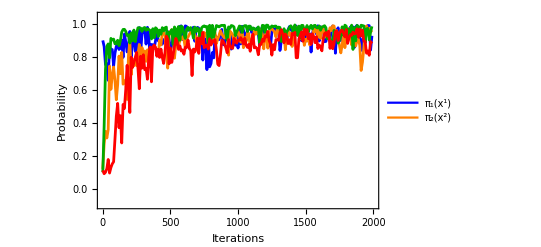

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists[[;;,1]]}];
data2 = Transpose[{iters,meanLists[[;;,2]]}];
data3 = Transpose[{iters,meanLists[[;;,3]]}];
data4 = Transpose[{iters,meanLists[[;;,4]]}];


p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,FrameLabel->{"Iterations","Probability"}],
ListPlot[data2,PlotStyle->Orange,PlotRange->Full,Joined->True],
ListPlot[data3,PlotStyle->Darker@Green,PlotRange->Full,Joined->True],
ListPlot[data4,PlotStyle->Red,PlotRange->Full,Joined->True]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(x^1)", "π_2(x^2)"}
]
,{0.8,0.2}]
]
```

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];
```

```mathematica
histEls={};

inputs = μ1;

prListUList ={};
prListList={};

a = 0.0;
aList ={};

Do[
prListU={};
prList={};
Do[

EjListt=EjListInit ;
BijListt=BijListInit;
FijListt=FijListInit;
WijMat = MapInputToWijMat[a*inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool];
histEls={};
Do[
oTree = OrientTree[trees[[m]],numOuts[[k,1]]];
AppendTo[histEls,TreeWeight[oTree,WijMat]]
,{m,1,Length[trees]}];
pr=(Total[histEls]^2/Total[histEls^2])/(Length[trees]);
AppendTo[prListU,pr];

EjListt=EjList;
BijListt=BijList;
FijListt=FijList;
WijMat = MapInputToWijMat[a*inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool];
histEls={};
Do[
oTree = OrientTree[trees[[m]],numOuts[[k,1]]];
AppendTo[histEls,TreeWeight[oTree,WijMat]]
,{m,1,Length[trees]}];
pr=(Total[histEls]^2/Total[histEls^2])/(Length[trees]);
AppendTo[prList,pr];


,{k,1,4}];

AppendTo[prListUList,prListU];
AppendTo[prListList,prList];
AppendTo[aList,a];
,{a,0,1,.1}];
```

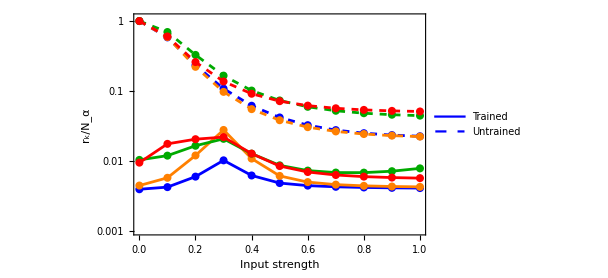

```mathematica
SetOptions[ListLogPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

lp=ListLogPlot;

cols = {Blue,Orange,Darker@Green,Red};

pList={};

Do[
data=Transpose[{aList,Transpose[prListList][[k]]}];
dataU=Transpose[{aList,Transpose[prListUList][[k]]}];
AppendTo[pList,
Show[
lp[data,PlotStyle->Directive[cols[[k]]],PlotRange->{0.001,1.1},Joined->True,
FrameLabel->{"Input strength", "r_k/N_α"},ImageSize->450],
lp[data,PlotStyle->Directive[cols[[k]]]],
lp[dataU,Joined->True,PlotStyle->Directive[cols[[k]],Dashed]],
lp[dataU,PlotStyle->Directive[cols[[k]]]]
]
];

,{k,1,4}];



 p=Show[Legended[pList,
Placed[LineLegend[{Directive[Blue],Directive[Blue,Dashed]},{"Trained","Untrained"},LabelStyle->{FontFamily->"Arial",FontSize->18}],{0.76,0.8}]]]

(*p=Show[pList]*)
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/DimensionalityPlotsP1Random.png",p];
```

```mathematica
GetTreeFrenesy[tree_,frenesies_]:=Module[
{weight, edge},
weight = 0;
Do[
edge = tree[[i]];
weight += frenesies[[Position[edges,edge][[1,1]]]];
,{i,1,Length[tree]}];
weight
]


EjListt=EjListInit ;
BijListt=BijListInit;
FijListt=FijListInit;

(*EjListt=EjList;
BijListt=BijList;
FijListt=FijList;*)


WijMat=MapInputToWijMat[0*inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool];
piVec = GetStationaryVector[WijMat];
frenesies = GetEdgeFrenesies[edges,nEdges,piVec,WijMat];
```

```mathematica
EjListt=EjListInit ;
BijListt=BijListInit;
FijListt=FijListInit;

EjListt=EjList;
BijListt=BijList;
FijListt=FijList;


tfs=GetTreeFrenesy[#,frenesies]&/@trees;

tfArray = {};
fm = 20;
m = 1;
del = 1;
distances = {};
μList = {μ1,μ2,μ3,μ4};
Do[
subdist={};
Do[
inputs = xyList[[μind]][[iter]];
WijMat=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool];
piVec = GetStationaryVector[WijMat];
frenesies = GetEdgeFrenesies[edges,nEdges,piVec,WijMat];
tfs=GetTreeFrenesy[#,frenesies]&/@trees;

(*distance = N[Norm[{F1,F2}-#]&/@{μ1,μ2,μ3,μ4}];*)
distance = Norm[inputs-μList[[μind]]];
AppendTo[subdist,distance];

AppendTo[tfArray,tfs->μind];
,{iter,1,200}];
AppendTo[distances,subdist];
,{μind,{1,2,3,4}}];
```

```mathematica
tfArrayInit = tfArray
```

```mathematica
tfArrayFin = tfArray
```

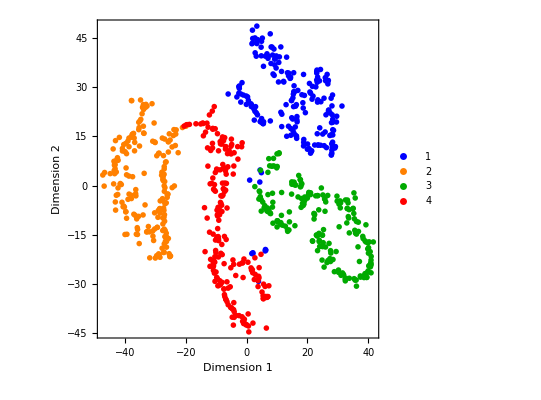

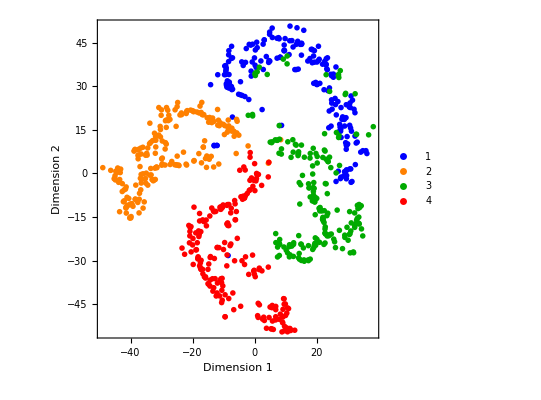

```mathematica
(*reducedInit= DimensionReduction[tfArrayInit[[All,1]],2,Method->{"TSNE","Perplexity"->40}];
reducedFin= DimensionReduction[tfArrayFin[[All,1]],2,Method->{"TSNE","Perplexity"->40}];*)

reducedInit= DimensionReduction[tfArrayInit[[All,1]],2,Method->{"TSNE","Perplexity"->10}];
reducedFin= DimensionReduction[tfArrayFin[[All,1]],2,Method->{"TSNE","Perplexity"->10}];

featuresInit=GroupBy[tfArrayInit,Last->First];
reducedfeaturesInit=reducedInit/@featuresInit;
pl=ListPlot[Values[reducedfeaturesInit],PlotLegends->Keys[reducedfeaturesInit],
PlotMarkers->{●,Medium},PlotStyle->{Blue,Orange,Darker@Green,Red},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"}]

featuresFin=GroupBy[tfArrayFin,Last->First];
reducedfeaturesFin=reducedFin/@featuresFin;
pl=ListPlot[Values[reducedfeaturesFin],PlotLegends->Keys[reducedfeaturesFin],
PlotMarkers->{●,Medium},PlotStyle->{Blue,Orange,Darker@Green,Red},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"}]
```

```mathematica
features=GroupBy[tfArray,Last->First];
reducedfeatures=reduced/@features;
ListPointPlot3D[Values[reducedfeatures]]
```

-Graphics3D-

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

features=GroupBy[tfArray,Last->First];
reducedfeatures=reduced/@features;
pl=ListPlot[Values[reducedfeatures],PlotLegends->Keys[reducedfeatures],
PlotMarkers->{●,Medium},PlotStyle->{Blue,Orange,Darker@Green,Red},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"}]
```

-Graphics-

```mathematica
pl=ListPlot[Values[reducedfeatures],PlotLegends->Keys[reducedfeatures],
PlotMarkers->{●},PlotStyle->{Table[Directive[Blue,AbsolutePointSize[10]],{i,1,100}],Orange,Darker@Green,Red},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"}]
```

-Graphics-

```mathematica
ListPlot[Values[reducedfeaturesFin][[1]]]
```

-Graphics-

```mathematica
sInitList = {};
sFinList = {};
Do[

reducedInit= DimensionReduction[tfArrayInit[[All,1]],2,Method->{"TSNE","Perplexity"->p}];
reducedFin= DimensionReduction[tfArrayFin[[All,1]],2,Method->{"TSNE","Perplexity"->p}];

reducedfeaturesInit=reducedInit/@featuresInit;
reducedfeaturesFin=reducedFin/@featuresFin;

sInit=ClusteringMeasurements[reducedfeaturesInit,"Silhouette"];
sFin=ClusteringMeasurements[reducedfeaturesFin,"Silhouette"];

AppendTo[sInitList,sInit];
AppendTo[sFinList, sFin];

,{p,Join[{1},Range[5,50,5]]}]
```

```mathematica
Join[{1},Range[5,50,5]]
```

{1,5,10,15,20,25,30,35,40,45,50}

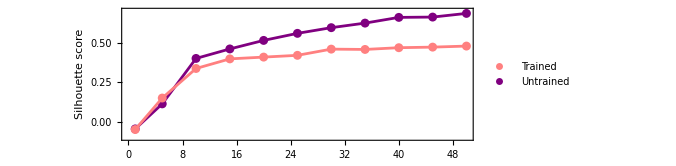

```mathematica
datInit = Transpose[{Join[{1},Range[5,50,5]],sInitList}];
datFin = Transpose[{Join[{1},Range[5,50,5]],sFinList}];
c1 = Purple;
c2 = Pink;
pl=Legended[
Show[
ListPlot[datInit,PlotStyle->c1,PlotRange->{-0.1,0.7},FrameLabel->{"Perplexity","Silhouette score"},AspectRatio->1/3,ImageSize->500],
ListPlot[datInit,PlotStyle->c1,Joined->True,PlotRange->Full],
ListPlot[datFin,PlotStyle->c2,PlotRange->Full],
ListPlot[datFin,PlotStyle->c2,Joined->True,PlotRange->Full]]
,
Placed[
PointLegend[{c2,c1},{"Trained","Untrained"},LabelStyle->{FontFamily->"Arial",FontSize->18}
]
,{0.8,0.25}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/PerplexityPlotRandom.png",pl,ImageResolution->300];
```

```mathematica
Keys[reducedfeatures]
```

{1,2,3,4}

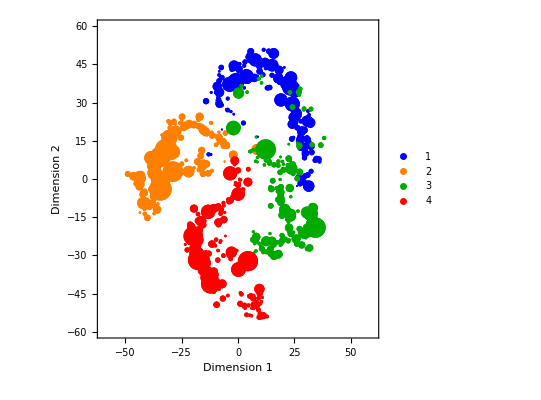

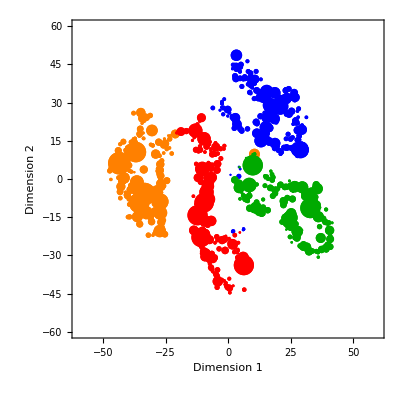

```mathematica
colors = {Blue,Orange,Darker@Green,Red};
plFin=Legended[

Show[Table[
ListPlot[Transpose[{Values[reducedfeaturesFin][[k]]}],PlotRange->3*{{-20,20},{-20,20}},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"},PlotStyle->Table[Directive[colors[[k]],●,PointSize[0.05*1/(distances[[k]][[i]]+1)]],{i,1,100}]],{k ,1,4}]
]
,
Placed[
PointLegend[colors,{"1","2","3","4"},LabelStyle->{FontFamily->"Arial",FontSize->18}
]
,{0.85,0.75}]

]


(*plInit=Legended[

Show[Table[
ListPlot[Transpose[{Values[reducedfeaturesInit][[k]]}],PlotRange->3*{{-20,20},{-20,20}},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"},PlotStyle->Table[Directive[colors[[k]],●,PointSize[0.05*1/(distances[[k]][[i]]+1)]],{i,1,100}]],{k ,1,4}]
]
,
Placed[
PointLegend[colors,{"1","2","3","4"},LabelStyle->{FontFamily->"Arial",FontSize->18}
]
,{0.85,0.75}]

]*)

plInit=Show[Table[
ListPlot[Transpose[{Values[reducedfeaturesInit][[k]]}],PlotRange->3*{{-20,20},{-20,20}},AspectRatio->1,FrameLabel->{"Dimension 1","Dimension 2"},PlotStyle->Table[Directive[colors[[k]],●,PointSize[0.05*1/(distances[[k]][[i]]+1)]],{i,1,100}]],{k ,1,4}]
]
```

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TSNEInitRandom.png",plInit,ImageResolution->300];
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TSNEFinRandom.png",plFin,ImageResolution->300];
```

```mathematica
fm = 1*20;
del =1*1;

m = 1;
lpd1 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[1]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd2 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[2]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd3 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[3]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd4 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[4]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
```

```mathematica
SetOptions[ListDensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];


epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[0.015],Blue]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[0.015],Orange]}},ContourShading->None][[1]];
epilog3=ListContourPlot[lpd3,Contours->{{0.5,Directive[Thickness[0.015],Darker@Green]}},ContourShading->None][[1]];
epilog4=ListContourPlot[lpd4,Contours->{{0.5,Directive[Thickness[0.015],Red]}},ContourShading->None][[1]];



min = 0;
max =1.0;
colf1=(Blend[{Directive[Lighter@Blue,Opacity[0.0]],Directive[Lighter@Blue,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf2=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Orange,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf3=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Green,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf4=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Red,Opacity[0.85]]},Rescale[#,{min,max}]]&);
(*colf=(ColorData[{"LakeColors",{max,min}}][#]&);*)

pD=Show[
ListDensityPlot[lpd1,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf1,PlotLegends->Placed[BarLegend[{colf1,{min,max}},LegendLabel->"π_1(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left],Epilog->{epilog1,epilog2,epilog3,epilog4}
],

ListDensityPlot[lpd2,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf2
,PlotLegends->Placed[BarLegend[{colf2,{min,max}},LegendLabel->"π_2(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListDensityPlot[lpd3,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf3
,PlotLegends->Placed[BarLegend[{colf3,{min,max}},LegendLabel->"π_3(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListDensityPlot[lpd4,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf4
,PlotLegends->Placed[BarLegend[{colf4,{min,max}},LegendLabel->"π_4(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListPlot[xy1[[1;;;;25]],PlotStyle->Directive[Blue,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy2[[1;;;;25]],PlotStyle->Directive[Orange,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy3[[1;;;;25]],PlotStyle->Directive[Darker@Green,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy4[[1;;;;25]],PlotStyle->Directive[Red,Opacity[1]],PlotMarkers->{Automatic,7}]
]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/RandomGraphFourClassClassification.png",pD];
```

```mathematica
(*scFac = 0.005;
arFac=0.12;
pFac = 0.15;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.02;
edgeMin = 0.003;*)

scFac = 0.001;
arFac=0.08;
pFac = 0.1;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.04;
edgeMin = 0.003;

pG1=DrawParamGraph[0*μ1,inputInds,signs,paramBool,numOuts,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList, scFac,arFac,arMin,edgeMin,pMin,pFac,nodeCol,edgeCol,{},False, False,600]
```

-5.63053

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TrainedGraphRandomFourClassParams.png",pG1];
```

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];
```

```mathematica
numOuts
```

{{6},{4},{3},{5}}

```mathematica
ind =numOuts[[1,1]];
Psi1=GetPsiVec[6,trees,EjList,BijList,FijList,uiαArray];
Psi2=GetPsiVec[4,trees,EjList,BijList,FijList,uiαArray];
Psi3=GetPsiVec[3,trees,EjList,BijList,FijList,uiαArray];
Psi4=GetPsiVec[5,trees,EjList,BijList,FijList,uiαArray];

PsiArray={Psi1,Psi2,Psi3,Psi4};

inputs = μ3;
Chi1=GetChiVec[6,trees,inputs,viαArray];
Chi2=GetChiVec[4,trees,inputs,viαArray];
Chi3=GetChiVec[3,trees,inputs,viαArray];
Chi4=GetChiVec[5,trees,inputs,viαArray];
ChiArray={Chi1,Chi2,Chi3,Chi4};
```

```mathematica
dotArray = ConstantArray[0,{4,4}];
inputsList = {μ1,μ2,μ3,μ4};
Do[
inputs=inputsList[[ci]];
Chi1=GetChiVec[6,trees,inputs,viαArray];
Chi2=GetChiVec[4,trees,inputs,viαArray];
Chi3=GetChiVec[3,trees,inputs,viαArray];
Chi4=GetChiVec[5,trees,inputs,viαArray];
ChiArray={Chi1,Chi2,Chi3,Chi4};
Do[
(*dotArray[[pi,ci]]=PsiArray[[pi]].ChiArray[[pi]];*)
dotArray[[pi,ci]]=Normalize[PsiArray[[pi]]].ChiArray[[pi]]
,{pi,1,4}],{ci,1,4}]
```

```mathematica
dotArray//MatrixForm
```

(5.10106×10^8 | 0.00085896 | 78957. | 66.3575
23905.5 | 470.548 | 507542. | 60634.9
6852.19 | 593.889 | 5.09468×10^8 | 31.7332
39118. | 0.118067 | 263752. | 527.567)

```mathematica
Map[Norm,PsiArray]//Normalize
```

{0.430989,0.900506,0.0529587,0.0230682}

```mathematica
Norm[ChiArray[[1]]]//N
```

1.38721×10^7

```mathematica
ArrayPlot[dotArray]
```

-Graphics-

```mathematica
Norm[Psi1]
```

9.3456×10^7

```mathematica
Norm[Psi3]
```

3.885×10^7

```mathematica
Psi1.Psi4
```

0.951844

#### Creased landscape

```mathematica
SeedRandom[38];

nNodes = 6;
nEdges = 15;
(*
g = CreateRandomGraph[nNodes,nEdges];*)

nNodes = 6;
g = CompleteGraph[nNodes];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];


Graph[g,VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexLabels->"Name"]
coords = GraphEmbedding[g]
```

-Graphics-

```mathematica
n=50000;  (*Sample size*)

off =0*{1,1};

fFac = 10;
off =0*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
μ2=1*fFac*{1,1}+fFac*off;
μ3=1*fFac*{-1,1}+fFac*off;
μ4=1*fFac*{1,-1}+fFac*off;


rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.4;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
xy3 = RandomVariate[BinormalDistribution[μ3,{sigma,sigma},rho],n];
xy4 = RandomVariate[BinormalDistribution[μ4,{sigma,sigma},rho],n];
th = -1*Pi/4;

rot = {{Cos[th],-Sin[th]},{Sin[th],Cos[th]}};
xy1 = (rot.#)&/@xy1;
xy2 = (rot.#)&/@xy2;
xy3 = (rot.#)&/@xy3;
xy4 = (rot.#)&/@xy4;


xyList = {xy1,xy2,xy3,xy4};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange],
ListPlot[xy3,PlotStyle->Darker@Green],
ListPlot[xy4,PlotStyle->Red]]
```

-Graphics-

```mathematica
RandomSeed[18];
(*RandomSeed[50];*)

nIter = 2000;
timeStride = 10; 

(*numOuts = {{6},{4},{3},{5}}; (* how many output nodes - for multiclass*)*)
numOuts = {{6},{4},{3},{1}}; (* how many output nodes - for multiclass*)
(*inputInds={{7},{11}}; (* which input edges *)*)
inputInds={{5,14},{15,11}}; (* which input edges - for cirlce*)


repBool=False;
BijBool=False;
fth=5000*10^-1;

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
signs = {1,1};

deltaE=1;
deltaF=0.5;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]=-0;

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

(*EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;*)


outsLabels = GetOutsLabels[nNodes,numOuts];

meanLists = {};
stdLists = {};


Do[
nInd = RandomInteger[Length[numOuts]-1]+1;

inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre];

outsDiffs = outsLabels[[nInd]];
{piVecNudged,fluxesNudged,frenesiesNudged}=nudgedStationaryVector[inputs,inputInds,signs,numOuts,deltaE*outsDiffs,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList,BijBool,repBool];

pisDiffs = piVecNudged -piVecPre;
EjList -= deltaF*pisDiffs;

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
FijList += deltaF*fluxesDiffs;
FijList=Clip[FijList,{-fth,fth}];

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
BijList += deltaF*fluxesDiffs;

If[Mod[iter,timeStride]==0,
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];
];

,{iter,1,nIter}];

Print["Done."]
```

Done.

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists[[;;,1]]}];
data2 = Transpose[{iters,meanLists[[;;,2]]}];
data3 = Transpose[{iters,meanLists[[;;,3]]}];
data4 = Transpose[{iters,meanLists[[;;,4]]}];


p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,FrameLabel->{"Iterations","Probability"}],
ListPlot[data2,PlotStyle->Orange,PlotRange->Full,Joined->True],
ListPlot[data3,PlotStyle->Darker@Green,PlotRange->Full,Joined->True],
ListPlot[data4,PlotStyle->Red,PlotRange->Full,Joined->True]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(x^1)", "π_2(x^2)"}
]
,{0.8,0.2}]
]
```

-Graphics-

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];
```

```mathematica
{EjListt, BijListt, FijListt}=RandomInitialParameters[0,0,0,nNodes,nEdges];
(*{EjListt, BijListt, FijListt}={EjList, BijList, FijList};*)

LSE[x_,y_,l_]:=Evaluate[GetLSE[nNodes,trees,EjListt,BijListt,FijListt,{xx,yy},uiαArray,viαArray,1]+ l*1/2(xx*xx+yy*yy)/.{xx->x,yy->y}] ;
piF[x_,y_]:=Evaluate[GetpiVecTrees[nNodes,trees,EjListt,BijListt,FijListt,{xx,yy},uiαArray,viαArray]/.{xx->x,yy->y}];
lap[x_,y_]:=Evaluate[Laplacian[LSE[xx,yy,0],{xx,yy}]/.{xx->x,yy->y}];
gradLSE[x_,y_]:=Evaluate[Grad[LSE[xx,yy,0],{xx,yy}]/.{xx->x,yy->y}];
ent[x_,y_]:=-piF[x,y].Log[piF[x,y]];
lapEnt[x_,y_]:=Evaluate[Laplacian[ent[xx,yy],{xx,yy}]/.{xx->x,yy->y}];
gradpi[x_,y_]:=Evaluate[Grad[Log[piF[xx,yy]],{xx,yy}]/.{xx->x,yy->y}];
lappi[x_,y_]:=Evaluate[Laplacian[Log[piF[xx,yy]],{xx,yy}]/.{xx->x,yy->y}];

LNumk[x_,y_]:=Evaluate[GetLNumk[nNodes,trees,EjListt,BijListt,FijListt,{xx,yy},uiαArray,viαArray,1]/.{xx->x,yy->y}] ;
lapLNumk[x_,y_]:=Evaluate[Laplacian[LNumk[xx,yy],{xx,yy}]/.{xx->x,yy->y}];
gradLNumk[x_,y_]:=Evaluate[Grad[LNumk[xx,yy],{xx,yy}]/.{xx->x,yy->y}];
```

```mathematica
SetOptions[Plot3D,
Axes->True,
AxesStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

min = -0.3;
max = 0;
colf=(ColorData[{"FuchsiaTones",{min,max}}][#]&);
ki=1;
m = 4;
p=Plot3D[LSE[Fa,Fb,0],{Fa,-m*20,m*20},{Fb,-m*20,m*20},AxesLabel->{"F_a","F_b","ℱ"},PlotLegends->False,PlotRange->{-190,0},
ColorFunction->Function[{x,y,z},ColorData["FuchsiaTones"][Rescale[lap[x,y],{min,max}]]],
(*p=Plot3D[LNumk[Fa,Fb][[ki]],{Fa,-m*20,m*20},{Fb,-m*20,m*20},AxesLabel->{"F_a","F_b","ℱ"},PlotLegends->False,PlotRange->{-170,0},
ColorFunction->Function[{x,y,z},ColorData["FuchsiaTones"][Rescale[lapLNumk[x,y][[ki]],{min,max}]]],*)
ColorFunctionScaling->False,
Boxed->False,
PlotPoints->100,
ViewPoint->{1.3,-2.4,2.5},
AspectRatio->1, ImageSize->Large];

p3=Legended[p,BarLegend[{"FuchsiaTones",{min,max}},LabelStyle->Directive[Black,18],LegendLabel->"∇^2 ℱ"]]
```

-Graphics3D-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/Creased3DUntrained.png",p3];
```

```mathematica
SetOptions[ListDensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];


epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[0.015],Blue]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[0.015],Orange]}},ContourShading->None][[1]];
epilog3=ListContourPlot[lpd3,Contours->{{0.5,Directive[Thickness[0.015],Darker@Green]}},ContourShading->None][[1]];
epilog4=ListContourPlot[lpd4,Contours->{{0.5,Directive[Thickness[0.015],Red]}},ContourShading->None][[1]];



min = 0;
max =1.0;
colf1=(Blend[{Directive[Lighter@Blue,Opacity[0.0]],Directive[Lighter@Blue,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf2=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Orange,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf3=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Green,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf4=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Red,Opacity[0.85]]},Rescale[#,{min,max}]]&);
(*colf=(ColorData[{"LakeColors",{max,min}}][#]&);*)

pD=Show[
ListDensityPlot[lpd1,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf1,PlotLegends->Placed[BarLegend[{colf1,{min,max}},LegendLabel->"π_1(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left],Epilog->{epilog1,epilog2,epilog3,epilog4}
],

ListDensityPlot[lpd2,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf2
,PlotLegends->Placed[BarLegend[{colf2,{min,max}},LegendLabel->"π_2(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListDensityPlot[lpd3,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf3
,PlotLegends->Placed[BarLegend[{colf3,{min,max}},LegendLabel->"π_3(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListDensityPlot[lpd4,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf4
,PlotLegends->Placed[BarLegend[{colf4,{min,max}},LegendLabel->"π_4(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListPlot[xy1[[1;;;;50]],PlotStyle->Directive[Blue,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy2[[1;;;;50]],PlotStyle->Directive[Orange,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy3[[1;;;;50]],PlotStyle->Directive[Darker@Green,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy4[[1;;;;50]],PlotStyle->Directive[Red,Opacity[1]],PlotMarkers->{Automatic,7}]
]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/HexGraphFourClassClassificationRot.png",pD];
```

```mathematica
SetOptions[ContourPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

m =4(*Sqrt[2]*);
(*m = Sqrt[2];*)


min = -0.3;
max = 0.00;
colf=(ColorData[{"FuchsiaTones",{min,max}}][#]&);

th =0.01;
epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[th],Blue]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[th],Orange]}},ContourShading->None][[1]];
epilog3=ListContourPlot[lpd3,Contours->{{0.5,Directive[Thickness[th],Darker@Green]}},ContourShading->None][[1]];
epilog4=ListContourPlot[lpd4,Contours->{{0.5,Directive[Thickness[th],Red]}},ContourShading->None][[1]];

pD=Show[
DensityPlot[lap[Fa,Fb],{Fa,-m*20,m*20},{Fb,-m*20,m*20},PlotRange->{min,max},
ColorFunction->colf,
ColorFunctionScaling->False,
PlotPoints->200,
ClippingStyle->{colf[min],colf[max]},
PlotLegends->BarLegend[{colf,{min,max}},LegendLabel->"∇^2 ℱ"],
FrameLabel->{"F_a","F_b"},
Epilog->{First[ContourPlot[LSE[Fa,Fb,0],{Fa,-m*20,m*20},{Fb,-m*20,m*20},Contours->10,ContourShading->None,ContourStyle->Directive[Black,Dashed,Opacity[0.75]]]](*,epilog1,epilog2,epilog3,epilog4*)}]
]
```

-Graphics-

```mathematica
colf[-0.3]
```

RGBColor[0.1, 0.1, 0.1]

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/LaplacianDecisionBoundaryZoomout.png",pD];
```

```mathematica
SetOptions[ContourPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

m =Sqrt[2];
min = 0;
max = 1.5;
colf=(ColorData[{"LakeColors",{min,max}}][1-#]&);

th =0.01;
epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[th],Blue]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[th],Orange]}},ContourShading->None][[1]];
epilog3=ListContourPlot[lpd3,Contours->{{0.5,Directive[Thickness[th],Darker@Green]}},ContourShading->None][[1]];
epilog4=ListContourPlot[lpd4,Contours->{{0.5,Directive[Thickness[th],Red]}},ContourShading->None][[1]];

pD=Show[
DensityPlot[ent[Fa,Fb],{Fa,-m*20,m*20},{Fb,-m*20,m*20},PlotRange->{min,max},
ColorFunction->colf,
ColorFunctionScaling->False,
PlotPoints->200,
PlotLegends->BarLegend[{colf,{min,max}},LegendLabel->"S[π]"],
FrameLabel->{"F_a","F_b"},

Epilog->{First[ContourPlot[ent[Fa,Fb],{Fa,-m*20,m*20},{Fb,-m*20,m*20},Contours->10,PlotPoints->100,ContourShading->None,ContourStyle->Directive[Black,Dashed,Opacity[0.75]]]],epilog1,epilog2,epilog3,epilog4}]
]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/EntropyPlotTrained.png",pD];
```

```mathematica
m = 8;

arrows = {};(* will be a list of Graphics objects containing arrows *)
maxNorm=1;
scale = 15;
opScale =0.5;(* controls the opacity, to use inside opacity = Log[Subscript[v, mag] * opScale]; you can change you want to control the opacity below *)
color=Black; (* arrow color *)
ah = 0.02; (* size of the arrow heads *)
del = 20;

Do[
Do[
p1={Fa,Fb};
grad = gradLSE[Fa,Fb];
gNorm = Norm[grad]+10^-6;
p2=p1+scale*grad/gNorm;

(*op = opScale*gNorm/maxNorm;*)
op = 1;


AppendTo[arrows,Graphics[{Black,Opacity[op],Arrowheads[ah],Arrow[{p1,p2}]}]] (* add this arrow to the list *)

,{Fa,-m*fm,m*fm,del}],
{Fb,-m*fm,m*fm,del}];

pSim=Show[arrows,ImageSize->300]

(*
VectorPlot[gradLSE[Fa,Fb],{Fa,-m*20,m*20},{Fb,-m*20,m*20},VectorStyle->Black]*)
```

-Graphics-

```mathematica
SetOptions[ContourPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

polarAngle[Fa_,Fb_]:=ArcTan[gradLSE[Fa,Fb][[1]]+10^-6,gradLSE[Fa,Fb][[2]]+10^-6]


pV=Show[
DensityPlot[polarAngle[x,y],{x,-m*fm,m*fm},{y,-m*fm,m*fm},
PlotPoints->200,ColorFunction->Function[{angle},Opacity[0.5,Hue[Rescale[angle,{-Pi,Pi}]]]],
ColorFunctionScaling->False,
PlotRange->All,
PlotLegends->BarLegend[{Automatic,{-Pi-0.01,Pi+0.01}},LegendLabel->"Angle",Ticks->(Table[{i*Pi,ToString@TraditionalForm[i*Pi]},{i,-1,1,1/2}])],
FrameLabel->{"F_a","F_b"}]
,arrows]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/GradLnZVecUntrained.png",pV];
```

```mathematica
fm = 1*20;
del =2*1;

(*{EjListt, BijListt, FijListt}=RandomInitialParameters[0,0,0,nNodes,nEdges];*)
{EjListt, BijListt, FijListt}={EjList, BijList, FijList};

m = Sqrt[2];
lpd1 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool][[1]]]},{F1,-m*fm,m*fm,del},{F2,-m*fm,m*fm,del}],1];
lpd2 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool][[2]]]},{F1,-m*fm,m*fm,del},{F2,-m*fm,m*fm,del}],1];
lpd3 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool][[3]]]},{F1,-m*fm,m*fm,del},{F2,-m*fm,m*fm,del}],1];
lpd4 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjListt, BijListt, FijListt,BijBool,repBool][[4]]]},{F1,-m*fm,m*fm,del},{F2,-m*fm,m*fm,del}],1];
```

```mathematica
(*scFac = 0.02;
arFac=0.08;
pFac = 0.1;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.04;
edgeMin = 0.003;*)
vCoords = Table[i->coords[[i]],{i,1,nNodes}];

scFac = 0.001;
arFac=0.08;
pFac = 0.1;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.05;
edgeMin = 0.002;

pG1=DrawParamGraph[μ1,inputInds,signs,paramBool,numOuts,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList, scFac,arFac,arMin,edgeMin,pMin,pFac,nodeCol,edgeCol,vCoords,False]
```

-5.88762

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TrainedGraphHexFourClassParamsRot.png",pG1];
```

```mathematica
BijList
```

{0.519431,2.24906,2.7559,-2.53124,-5.88762,1.81686,1.45647,-1.82277,1.10163,3.30843,-1.02999,3.38066,-1.50115,-4.75436,0.93869}

```mathematica
FijList
```

{0.470861,-1.1672,-0.435395,-2.75924,7.36303,-0.229037,-0.971886,-1.56849,-1.09937,-0.0739199,-4.66812,-1.38974,3.8691,-3.67608,-4.59991}

```mathematica
mb=Max[BijList]
```

3.38066

```mathematica
BijList[[-3]]/mb+edgeMin
```

-0.44354

```mathematica
edges
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6}

```mathematica
Graph[g,VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexLabels->"Name"]
coords = GraphEmbedding[g]
```

-Graphics-

{{-0.866025,0.5},{-0.866025,-0.5},{3.82857×10^-16,-1.},{0.866025,-0.5},{0.866025,0.5},{1.83697×10^-16,1.}}

#### Vector space

```mathematica
SeedRandom[38];

nNodes = 6;
nEdges = 15;
(*
g = CreateRandomGraph[nNodes,nEdges];*)

nNodes = 6;
g = CompleteGraph[nNodes];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];


Graph[g,VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexLabels->"Name"]
coords = GraphEmbedding[g]
```

-Graphics-

{{-0.866025,0.5},{-0.866025,-0.5},{3.82857×10^-16,-1.},{0.866025,-0.5},{0.866025,0.5},{1.83697×10^-16,1.}}

```mathematica
n=50000;  (*Sample size*)

fFac = 10;
off =0*{1,1};
μ1 =1*fFac*{-1,-1} +fFac*off;
(*μ2=1*fFac*{0.5,1}+fFac*off;*)
μ2=1*fFac*{1,1}+fFac*off;
(*μ3=1*fFac*{-1,1}+fFac*off;
μ4=1*fFac*{1,-1}+fFac*off;*)

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.4;

xy1 = RandomVariate[BinormalDistribution[μ1,{sigma,sigma},rho],n];
xy2 = RandomVariate[BinormalDistribution[μ2,{sigma,sigma},rho],n];
(*xy3 = RandomVariate[BinormalDistribution[μ3,{sigma,sigma},rho],n];
xy4 = RandomVariate[BinormalDistribution[μ4,{sigma,sigma},rho],n];*)
xyList = {xy1,xy2,xy3,xy4};
(*labels = {{1,-1,-1},{-1,1,-1},{-1,-1,1}};*)

Show[
ListPlot[xy1,PlotStyle->Blue,PlotRange->fFac*{{-2,2},{-2,2}}, FrameLabel->{"F_1","F_2"},AspectRatio->1],
ListPlot[xy2,PlotStyle->Orange]]
```

-Graphics-

```mathematica
edges[[11]]
```

3<->5

```mathematica
RandomSeed[36];

nIter = 500;
timeStride = 2; 

numOuts = {{6},{4}}; (* how many output nodes - for multiclass*)
(*inputInds={{7},{11}}; (* which input edges *)*)
inputInds={{5},{11}}; (* which input edges - for cirlce*)

repBool=False;
BijBool=False;
fth=0*10^-1;

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
signs = {1,1};

deltaE=1;
deltaF=0.5;

EjList = ConstantArray[0,{nNodes}];
FijList = ConstantArray[0,{nEdges}];
BijList = ConstantArray[0,{nEdges}];
EjList[[Flatten[numOuts]]]=-0;

WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];

EjListInit = EjList;
BijListInit=BijList;
FijListInit=FijList;

EjListList={EjListInit};
BijListList={BijListInit};
FijListList={FijListInit};

outsLabels = GetOutsLabels[nNodes,numOuts];

meanLists = {};
stdLists = {};
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];

Do[
nInd = RandomInteger[Length[numOuts]-1]+1;

inputs = xyList[[nInd]][[iter]];
WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
piVecPre=GetStationaryVector[WijMatPre];

outsDiffs = outsLabels[[nInd]];
{piVecNudged,fluxesNudged,frenesiesNudged}=nudgedStationaryVector[inputs,inputInds,signs,numOuts,deltaE*outsDiffs,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList,BijBool,repBool];

pisDiffs = piVecNudged -piVecPre;
EjList -= deltaF*pisDiffs;

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,False,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
FijList += deltaF*fluxesDiffs;
FijList=Clip[FijList,{-fth,fth}];

piPrime=ComputepiAndPiprime[inputs, inputInds,signs,g,edges,nEdges,nNodes,True,EjList,BijList,FijList,adjMat,0.001,BijBool,repBool];
fluxesDiffs =(piVecNudged / piVecPre).piPrime;
BijList += deltaF*fluxesDiffs;

If[Mod[iter,timeStride]==0,
{newMeans, newStds}=TestPredictions[meanLists,stdLists,10,xyList,inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool];
AppendTo[meanLists,newMeans];
AppendTo[stdLists,newStds];

AppendTo[EjListList,EjList];
AppendTo[BijListList,BijList];
AppendTo[FijListList,FijList];

];

,{iter,1,nIter}];

Print["Done."]
```

Done.

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

iters = Range[0,Length[meanLists]-1]*timeStride;
data1 = Transpose[{iters,meanLists[[;;,1]]}];
data2 = Transpose[{iters,meanLists[[;;,2]]}];


p=Legended[
Show[
ListPlot[data1,PlotRange->{{0,nIter},{-0.1,1.05}},PlotStyle->Blue,Joined->True,ImageSize->500,FrameLabel->{"Iterations","Probability"}],
ListPlot[data2,PlotStyle->Orange,PlotRange->Full,Joined->True]
],
Placed[
LineLegend[{Blue,Orange},{"π_1(SuperscriptBox[StyleBox[\"F\",FontWeight->\"Bold\"], \"1\"])", "π_2(SuperscriptBox[StyleBox[\"F\",FontWeight->\"Bold\"], \"2\"])"},
(*LineLegend[{Blue,Orange},{"π_1(B^1)", "π_2(B^2)"},*)
Background->Directive[White,Opacity[0.75]],
LabelStyle->{FontFamily->"Arial",FontSize->20}
]
,{0.8,0.25}]
]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/ConvergenceHex.png",p];
```

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes,BijBool];
```

```mathematica
fm = 1*20;
del =1*1;

m = 1;
lpd1 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[1]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
lpd2 = Flatten[Table[{F1,F2,Mean[MapInputOutput[{F1,F2},inputInds,signs,numOuts,g,edges,nEdges,nNodes,adjMat,EjList, BijList, FijList,BijBool,repBool][[2]]]},{F1,-fm,m*fm,del},{F2,-fm,m*fm,del}],1];
```

```mathematica
edges[[inputInds[[2,1]]]]
```

3<->5

```mathematica
SetOptions[ListDensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];


epilog1=ListContourPlot[lpd1,Contours->{{0.5,Directive[Thickness[0.015],Blue]}},ContourShading->None][[1]];
epilog2=ListContourPlot[lpd2,Contours->{{0.5,Directive[Thickness[0.015],Orange]}},ContourShading->None][[1]];



min = 0;
max =1.0;
colf1=(Blend[{Directive[Lighter@Blue,Opacity[0.0]],Directive[Lighter@Blue,Opacity[0.85]]},Rescale[#,{min,max}]]&);
colf2=(Blend[{Directive[Lighter@Orange,Opacity[0.0]],Directive[Lighter@Orange,Opacity[0.85]]},Rescale[#,{min,max}]]&);


pD=Show[
ListDensityPlot[lpd1,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf1,PlotLegends->Placed[BarLegend[{colf1,{min,max}},LegendLabel->"π_1(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left],Epilog->{epilog1,epilog2}
],

ListDensityPlot[lpd2,
FrameLabel->{"F_a","F_b"},PlotRange->{min,max},ColorFunctionScaling->False,ColorFunction->colf2
,PlotLegends->Placed[BarLegend[{colf2,{min,max}},LegendLabel->"π_2(StyleBox[\"F\",FontWeight->\"Bold\"])"],Left]
],

ListPlot[xy1[[1;;;;25]],PlotStyle->Directive[Blue,Opacity[1]],PlotMarkers->{Automatic,7}],

ListPlot[xy2[[1;;;;25]],PlotStyle->Directive[Orange,Opacity[1]],PlotMarkers->{Automatic,7}]
]
```

-Graphics-

```mathematica
(*Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/HexGraphFourClassClassification.png",pD];*)
```

```mathematica
(*scFac = 0.005;
arFac=0.12;
pFac = 0.15;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.02;
edgeMin = 0.003;*)

scFac = 0.01;
arFac=0.08;
pFac = 0.1;
paramBool = True;
nodeCol = {Black,Black};
edgeCol = Blue;
arMin = 0.0;
pMin = 0.04;
edgeMin = 0.003;
vCoords = Table[i->coords[[i]],{i,1,nNodes}];

pG1=DrawParamGraph[μ1,inputInds,signs,paramBool,numOuts,g,edges,nEdges,nNodes,adjMat,EjList,BijList,FijList, scFac,arFac,arMin,edgeMin,pMin,pFac,nodeCol,edgeCol,vCoords,False]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TrainedGraphHexFourClassParams.png",pG1];
```

```mathematica
trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes,BijBool];
```

```mathematica
(*ind =numOuts[[1,1]];
Psi1=GetPsiVec[6,trees,EjList,BijList,FijList,uiαArray];
Psi2=GetPsiVec[4,trees,EjList,BijList,FijList,uiαArray];

PsiArray={Psi1,Psi2};

inputs = μ3;
Chi1=GetChiVec[6,trees,inputs,viαArray];
Chi2=GetChiVec[4,trees,inputs,viαArray];
ChiArray={Chi1,Chi2};

dotArray = ConstantArray[0,{2,2}];
inputsList = {μ1,μ2};
ChiArrayList = {};
Do[
inputs=inputsList[[ci]];
Chi1=GetChiVec[6,trees,inputs,viαArray];
Chi2=GetChiVec[4,trees,inputs,viαArray];
ChiArray={Chi1,Chi2};
AppendTo[ChiArrayList,ChiArray];
Do[
(*dotArray[[pi,ci]]=PsiArray[[pi]].ChiArray[[pi]];*)
dotArray[[pi,ci]]=Normalize[PsiArray[[pi]]].Normalize[ChiArray[[pi]]]
,{pi,1,2}],{ci,1,2}]*)
```

```mathematica
proj1List={};
proj2List={};
u=GetChiVec[6,trees,μ1,viαArray]//Normalize;
v=GetChiVec[4,trees,μ2,viαArray]//Normalize;
(*{u,v}=Orthogonalize[{u,v}];*)

uo=GetChiVec[6,trees,μ2,viαArray]//Normalize;
vo=GetChiVec[4,trees,μ1,viαArray]//Normalize;
(*{u,v}=Orthogonalize[{u,v}];*)

projList={};
Do[
EjListt=EjListList[[t]];
BijListt=BijListList[[t]];
FijListt=FijListList[[t]];


(*pVec = GetPsiVec[6,trees,EjListt,BijListt,FijListt,uiαArray];
projVec=(pVec.u)*u+(pVec.v)*v;
AppendTo[proj1List,Norm[projVec]/Norm[pVec]];*)

(*pVec = GetPsiVec[4,trees,EjListt,BijListt,FijListt,uiαArray];
projVec=(pVec.u)*u+(pVec.v)*v;
AppendTo[proj2List,Norm[projVec]/Norm[pVec]];*)

pVec = GetPsiVec[6,trees,EjListt,BijListt,FijListt,uiαArray]//Normalize;
AppendTo[projList,{pVec.u,pVec.v,pVec.uo,pVec.vo}]


,{t,1,Length[EjListList]}]
```

```mathematica
OverTilde[ψ]
```

ψ̃

```mathematica
af=180/Pi;
d1=Transpose[{iters,af*ArcCos[projList[[;;,1]]]}];
d2=Transpose[{iters,af*ArcCos[projList[[;;,2]]]}];
d3=Transpose[{iters,af*ArcCos[projList[[;;,3]]]}];
d4=Transpose[{iters,af*ArcCos[projList[[;;,4]]]}];
p=ListPlot[{d1,d3,d4,d2},Joined->True,PlotRange->Full,PlotStyle->{Directive[Blue],Directive[Blue,Dashed],Directive[Orange,Dashed],Directive[Orange]},FrameLabel->{"Iterations","∠(ψ̃,χ) °"},ImageSize->500,PlotLegends->{"χ(1,F^1)","χ(1,F^2)","χ(2,F^1)","χ(2,F^2)"}]
```

-Graphics-

```mathematica
(*Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/ConvergenceHexAnglesVS.png",p];*)
```

```mathematica
(5/6)//N
```

0.833333

```mathematica
u=GetChiVec[6,trees,μ1,viαArray](*//Normalize*);
v=GetChiVec[4,trees,μ2,viαArray](*//Normalize*);
(*{u,v}=Orthogonalize[{u,v}];*)

uo=GetChiVec[6,trees,μ2,viαArray](*//Normalize*);
vo=GetChiVec[4,trees,μ1,viαArray](*//Normalize*);

projList={};
Do[
EjListt=EjListList[[t]];
BijListt=BijListList[[t]];
FijListt=FijListList[[t]];



(*pVec1 = GetPsiVec[6,trees,EjListt,BijListt,FijListt,uiαArray](*//Normalize*);
pVec2 = GetPsiVec[4,trees,EjListt,BijListt,FijListt,uiαArray](*//Normalize*);
AppendTo[projList,{pVec1.u,pVec1.uo,pVec2.v,pVec2.vo}]*)

pVec1 = GetPsiVec[1,trees,EjListt,BijListt,FijListt,uiαArray](*//Normalize*);
pVec2 = GetPsiVec[2,trees,EjListt,BijListt,FijListt,uiαArray](*//Normalize*);
pVec3 = GetPsiVec[3,trees,EjListt,BijListt,FijListt,uiαArray](*//Normalize*);
pVec4 = GetPsiVec[4,trees,EjListt,BijListt,FijListt,uiαArray](*//Normalize*);
pVec5 = GetPsiVec[5,trees,EjListt,BijListt,FijListt,uiαArray](*//Normalize*);
pVec6 = GetPsiVec[6,trees,EjListt,BijListt,FijListt,uiαArray](*//Normalize*);
(*AppendTo[projList,{pVec1.u,pVec2.u,pVec3.u,pVec4.u,pVec5.u,pVec6.u,
pVec1.v,pVec2.v,pVec3.v,pVec4.v,pVec5.v,pVec6.v}]*)

AppendTo[projList,{pVec6.u,pVec6.uo,pVec4.vo,pVec4.v}]



,{t,1,Length[EjListList]}]
```

```mathematica
t = 10;
EjListt=EjListList[[t]];
BijListt=BijListList[[t]];
FijListt=FijListList[[t]];
pi[b1_,b2_]:=Evaluate[GetpiVecTrees[nNodes,trees,EjListt,BijListt,FijListt,{b1t,b2t},uiαArray,viαArray]/.{b1t->b1, b2t->b2}]
```

```mathematica
Plot3D[pi[b1,b2][[6]],{b1,-20,20},{b2,-20,20}]
```

-Graphics3D-

```mathematica
af=180/Pi;
(*d1=Transpose[{iters,af*ArcCos[projList[[;;,1]]]}];
d2=Transpose[{iters,af*ArcCos[projList[[;;,2]]]}];
d3=Transpose[{iters,af*ArcCos[projList[[;;,3]]]}];
d4=Transpose[{iters,af*ArcCos[projList[[;;,4]]]}];*)
d1=Transpose[{iters,Log[projList[[;;,1]]]}];
d2=Transpose[{iters,Log[projList[[;;,2]]]}];
d3=Transpose[{iters,Log[projList[[;;,3]]]}];
d4=Transpose[{iters,Log[projList[[;;,4]]]}];
(*d5=Transpose[{iters,Log[projList[[;;,5]]]}];
d6=Transpose[{iters,Log[projList[[;;,6]]]}];

d7=Transpose[{iters,Log[projList[[;;,7]]]}];
d8=Transpose[{iters,Log[projList[[;;,8]]]}];
d9=Transpose[{iters,Log[projList[[;;,9]]]}];
d10=Transpose[{iters,Log[projList[[;;,10]]]}];
d11=Transpose[{iters,Log[projList[[;;,11]]]}];
d12=Transpose[{iters,Log[projList[[;;,12]]]}];*)
(*p=ListPlot[{d1,d2,d3,d4,d5,d6,d7,d8,d9,d10,d11,d12},Joined->True,PlotRange->Full,FrameLabel->{"Iterations","ln(ψ*χ)"},ImageSize->500,PlotStyle->{Black,Black,Black,Black,Black,Blue,Black,Black,Black,Orange,Black,Black}]*)
p=ListPlot[{d1,d3,d2,d4},Joined->True,PlotRange->Full,FrameLabel->{"Iterations","ln(ψ*χ)"},ImageSize->500,PlotStyle->{Directive[Blue],Directive[Blue,Dashed],Directive[Orange,Dashed],Directive[Orange]},
(*PlotLegends->{"ψ(1,θ)*χ(1,B^1)","ψ(2,θ)*χ(2,B^1)","ψ(1,θ)*χ(1,B^2)","ψ(2,θ)*χ(2,B^2)"}*)
(*PlotLegends->{"ψ(1,θ)*χ(1,B^1)","ψ(2,θ)*χ(2,B^1)","ψ(1,θ)*χ(1,B^2)","ψ(2,θ)*χ(2,B^2)"}*)
PlotLegends->{"StyleBox[\"ψ\",FontWeight->\"Bold\"]StyleBox[\"(\",FontWeight->\"Plain\"]StyleBox[\"1\",FontWeight->\"Plain\"]StyleBox[\",\",FontWeight->\"Plain\"]StyleBox[\"θ\",FontWeight->\"Bold\"])StyleBox[\"*\",FontWeight->\"Plain\"]StyleBox[\"χ\",FontWeight->\"Bold\"](1,SuperscriptBox[StyleBox[\"F\",FontWeight->\"Bold\"], \"1\"])","StyleBox[\"ψ\",FontWeight->\"Bold\"]StyleBox[\"(\",FontWeight->\"Plain\"]StyleBox[\"2\",FontWeight->\"Plain\"]StyleBox[\",\",FontWeight->\"Plain\"]StyleBox[\"θ\",FontWeight->\"Bold\"])StyleBox[\"*\",FontWeight->\"Plain\"]StyleBox[\"χ\",FontWeight->\"Bold\"](2,SuperscriptBox[StyleBox[\"F\",FontWeight->\"Bold\"], \"1\"])","StyleBox[\"ψ\",FontWeight->\"Bold\"]StyleBox[\"(\",FontWeight->\"Plain\"]StyleBox[\"1\",FontWeight->\"Plain\"]StyleBox[\",\",FontWeight->\"Plain\"]StyleBox[\"θ\",FontWeight->\"Bold\"])StyleBox[\"*\",FontWeight->\"Plain\"]StyleBox[\"χ\",FontWeight->\"Bold\"](1,SuperscriptBox[StyleBox[\"F\",FontWeight->\"Bold\"], \"2\"])","StyleBox[\"ψ\",FontWeight->\"Bold\"]StyleBox[\"(\",FontWeight->\"Plain\"]StyleBox[\"2\",FontWeight->\"Plain\"]StyleBox[\",\",FontWeight->\"Plain\"]StyleBox[\"θ\",FontWeight->\"Bold\"])StyleBox[\"*\",FontWeight->\"Plain\"]StyleBox[\"χ\",FontWeight->\"Bold\"](2,SuperscriptBox[StyleBox[\"F\",FontWeight->\"Bold\"], \"2\"])"}]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/ConvergenceHexDotVS.png",p];
```

```mathematica
{pVec1.u,pVec1.uo,pVec2.v,pVec2.vo}
```

```mathematica
af=180/Pi;
(*d1=Transpose[{iters,af*ArcCos[projList[[;;,1]]]}];
d2=Transpose[{iters,af*ArcCos[projList[[;;,2]]]}];
d3=Transpose[{iters,af*ArcCos[projList[[;;,3]]]}];
d4=Transpose[{iters,af*ArcCos[projList[[;;,4]]]}];*)
d1=Transpose[{iters,Log[projList[[;;,1]]]}];
d2=Transpose[{iters,Log[projList[[;;,2]]]}];
d3=Transpose[{iters,Log[projList[[;;,3]]]}];
d4=Transpose[{iters,Log[projList[[;;,4]]]}];
p=ListPlot[{d1,d2,d3,d4},Joined->True,PlotRange->Full,PlotStyle->{Directive[Blue],Directive[Blue,Dashed],Directive[Orange,Dashed],Directive[Orange]},FrameLabel->{"Iterations","∠(ψ̃,χ) °"},ImageSize->500,PlotLegends->{"χ(1,F^1)","χ(1,F^2)","χ(2,F^1)","χ(2,F^2)"}]
```

-Graphics-

```mathematica
Blend[{Blue,Orange}]
```

RGBColor[Rational[1, 2], 0.25, Rational[1, 2]]

```mathematica
0.25*255
```

63.75

#### Entanglements

```mathematica
SetOptions[ListDensityPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.002]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

dataSPP={{4,6},{8,28},{12,66},{16,120},{20,190}};
dataladder={{4,6},{7,32.1429},{10,156.8},{13,723.462},{16,3217.5},{19,13942.2}};

pE=Show[
ListLogPlot[{dataSPP,dataladder},PlotStyle->{Blue,Red},FrameLabel->{"Number of edges","Entangelement"}],
ListLogPlot[{dataSPP,dataladder},Joined->True,PlotStyle->{Blue,Red},PlotLegends->Placed[{"Serial push-pull","Ladder"},{0.3,0.8}]]
]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/Entanglements.png",pE,ImageResolution->300];
```

#### Classification schematics

```mathematica
n=125;  (*Sample size*)

fFac = 20;
off =1*{0,0,0};
μ1 =1*fFac*{-1,-1,-1} +fFac*off;
μ2=1*fFac*{1,1,1}+fFac*off;
μ3=1*fFac*{0.5,-1,1}+fFac*off;
μ4=1*fFac*{-1,1,-1}+fFac*off;
μ5=1*fFac*{1,-1,-1}+fFac*off;
μ6=1*fFac*{1,1,-1}+fFac*off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.8;
Σ=DiagonalMatrix[{sigma,sigma,sigma}];

xy1 = RandomVariate[MultinormalDistribution[μ1,Σ],n];
xy2 =RandomVariate[MultinormalDistribution[μ2,Σ],n];
xy3 =RandomVariate[MultinormalDistribution[μ3,Σ],n];
xy4 =RandomVariate[MultinormalDistribution[μ4,Σ],n];
xy5 =RandomVariate[MultinormalDistribution[μ5,Σ],n];
xy6 =RandomVariate[MultinormalDistribution[μ6,Σ],n];
xyList = {xy1,xy2};

op =0.9;
op2 = 0.1;
pr=32;
ps = 0.012;

ps=Show[
ListPointPlot3D[{xy1,xy2,xy3,xy4,xy5,xy6},PlotRange->{{-pr,pr},{-pr,pr},{-pr,pr}},AspectRatio->1,PlotStyle->{
Directive[Blue,Specularity[0.4],Opacity[op],PointSize[ps]],
Directive[Orange,Specularity[0.4],Opacity[op],PointSize[ps]] ,
Directive[Darker@Green,Specularity[0.4],Opacity[op],PointSize[ps]],
Directive[Red,Specularity[0.4],Opacity[op],PointSize[ps]],
Directive[Purple,Specularity[0.4],Opacity[op],PointSize[ps]],
Directive[Pink,Specularity[0.4],Opacity[op],PointSize[ps]]},
Boxed->False,Axes->Automatic,Ticks->None,AxesStyle->Directive[Black,Thickness[0.004]],ImagePadding->80,ImageSize->500,(*AxesLabel->{"Enzyme 1","Enzyme 2","Enzyme 3"},*)LabelStyle->{FontFamily->"Arial",FontSize->18}],
Graphics3D[{Directive[Blue,Opacity[op2]],Ellipsoid[μ1,Diagonal[Σ]/2]}],
Graphics3D[{Directive[Orange,Opacity[op2]],Ellipsoid[μ2,Diagonal[Σ]/2]}],
Graphics3D[{Directive[Darker@Green,Opacity[op2]],Ellipsoid[μ3,Diagonal[Σ]/2]}],
Graphics3D[{Directive[Red,Opacity[op2]],Ellipsoid[μ4,Diagonal[Σ]/2]}],
Graphics3D[{Directive[Purple,Opacity[op2]],Ellipsoid[μ5,Diagonal[Σ]/2]}],
Graphics3D[{Directive[Pink,Opacity[op2]],Ellipsoid[μ6,Diagonal[Σ]/2]}]
]
```

-Graphics3D-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/MultiClass3D.png",ps,ImageResolution->300];
```

```mathematica
n=25;  (*Sample size*)

fFac = 2.5;
off =fFac*0;
μ1 =1*fFac*(-1)+off;
μ2=1*fFac*(1)+off;

rho=0.0;  (*Correlation coefficient*)
sigma=fFac*0.4;


xy1 = Transpose[{RandomVariate[NormalDistribution[-1*fFac+off,sigma],n]}];
xy2 = Transpose[{RandomVariate[NormalDistribution[1*fFac+off,sigma],n]}];
xyList = {xy1,xy2};
dat1=xy1[[1;;;;1]];
dat2=xy2[[1;;;;1]];
off = 0.0;
pdat1=Transpose[{Transpose[dat1][[1]],ConstantArray[1-off,Length[dat1]]}];
pdat2=Transpose[{Transpose[dat2][[1]],ConstantArray[0+off,Length[dat2]]}];

s=0.0175;
fth=0.004;
pD=Show[
ListPlot[{pdat1,pdat2},PlotStyle->{Directive[Blue,Opacity[1],PointSize[s]],Directive[Orange,Opacity[1],PointSize[s]]},PlotRange->{{-5,5},{-0.0,1.0}},Axes->True,Frame->False,Ticks->None,AxesStyle->Directive[Thickness[fth],Black],Method->{"AxesInFront"->False},AxesLabel->{"Enzyme","π_S"},LabelStyle->{FontFamily->"Arial",FontSize->16},ImageSize->400,PlotRangePadding->0.02],

Plot[(1-Tanh[x/2])/2,{x,-5,5},
FrameLabel->{"F_a","π"},PlotRange->{{-0.1,1.1}},PlotStyle->Black]

]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TwoClassSchem.png",pD,ImageResolution->300];
```

#### Golgi network

```mathematica
(*Adjustable parameters*)
m=6;  (*Number of rows*)
n=4;  (*Number of columns*)
xSpacing=1.5;  (*Horizontal separation*)
ySpacing=0.5;  (*Vertical separation*)

(*Create the grid graph using GridGraph*)
g=GridGraph[{m,n}];

(*Generate custom coordinates for the vertices*)
coords=Flatten[Table[{i*xSpacing,j*ySpacing},{i,0,n-1},{j,0,m-1}],1];

(*Draw the graph with custom vertex coordinates*)
Graph[g,VertexCoordinates->coords,VertexStyle->Black,VertexSize->0.15,EdgeStyle->Directive[Thickness[0.005],Opacity[1],Black],ImageSize->400]
```

-Graphics-

#### Spanning trees

```mathematica
SeedRandom[36];

nNodes = 6;
g = CompleteGraph[nNodes];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];



vCoords ={{2.414338857510769,2.6730841184543714},{3.358414451242318,2.145233239104118},{0.,0.7415366790746624},{4.062126795562653,0.},{1.2075950128356883,1.7101061964597284},{2.891192663049722,2.1136638140432984-0.2},{2.7970296424741217,1.2253661678290595},{2.052741453566191,0.9284742014900683},{3.280928360962754,3.167198403825711},{1.8886237097210505,1.557870850239414},{3.190148533075726,0.2082582333304872},{1.9856923593469946,2.0562928627263695},{1.101030246956482,1.1485726665657219},{3.692477285339926,0.9075770673501602},{2.46206329310155,1.7170007179729065}};
th=Pi;
Rot = {{Cos[th],-Sin[th]},{Sin[th],Cos[th]}};
rCoords=Table[Rot.vCoords[[i,;;]],{i,1,Length[vCoords]}];

Graph[g,VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[1]],ImageSize->Large,VertexLabelStyle->Directive[Black,22,Red],VertexCoordinates->None,VertexLabels->"Name"]
coords = GraphEmbedding[g];
vcoords = Table[i->coords[[i]],{i,1,Length[coords]}];
```

-Graphics-

```mathematica
Graph[g,VertexCoordinates->coords,EdgeStyle->Directive[Black,Thickness[0.008],Opacity[1]],ImageSize->150,VertexStyle->Directive[Black],VertexSize->0.1]
```

-Graphics-

```mathematica
Graph[ReverseGraph[OrientTree[trees[[760]],2]],VertexCoordinates->vcoords,EdgeStyle->Directive[Black,Thickness[0.008],Opacity[1],Arrowheads[0.15]],ImageSize->150,VertexStyle->Directive[Black],VertexSize->0.1]
```

-Graphics-

#### Mutual information

```mathematica
SeedRandom[36];

nNodes = 10;
nEdges = 13;
nNodes = 6;
nEdges = 13;
(*nNodes =6;
nEdges = 20;*)

(*g = CreateRandomGraph[nNodes,nEdges];*)
g = CreateFullGraph[nNodes];


nEdges = Length[EdgeList[g]];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];

colors = RotateLeft[ColorData[97,"ColorList"],1];
th = 0.004;

e1=Orange;

(*pg=GraphPlot[HighlightGraph[DirectedGraph[g,
EdgeStyle->Directive[Thickness[0.004],Black,Opacity[1],Arrowheads[0.04]],
VertexSize->Medium,
ImageSize->Large,
VertexStyle->Table[i->Directive[colors[[i]],Opacity[1]],{i,1,nNodes}]],
{Style[edges[[eNums[[1]]]][[2]]->edges[[eNums[[1]]]][[1]],Directive[Thickness[th],e1,Arrowheads[0.04]]],
Style[edges[[eNums[[1]]]][[1]]->edges[[eNums[[1]]]][[2]],Directive[Thickness[th],e1,Dashed,Arrowheads[0.04]]]
}],
PlotStyle->{FontSize->14}]*)

vCoords = {{-1,-1},{-1,1},{1,1},{1,-1}};
Graph[g,VertexLabels->"Name",VertexSize->0.1,VertexStyle->Table[i->Directive[colors[[i]],Opacity[1]],{i,1,nNodes}],EdgeStyle->Directive[Black,Thick,Opacity[0.75]],ImageSize->Medium]

vs = Table[i->0.1,{i,1,nNodes}]
vd=0.1;
vs = {1->2.5vd,2->2.5vd,3->vd,4->vd,5->vd,6->vd};
Graph[g,(*VertexLabels->"Name",*)VertexSize->vs,VertexStyle->Table[i->Directive[colors[[i]],Opacity[1]],{i,1,nNodes}],EdgeStyle->Directive[Black,Thickness[0.008],Opacity[0.75]],ImageSize->75]
```

-Graphics-

{1→0.1,2→0.1,3→0.1,4→0.1,5→0.1,6→0.1}

-Graphics-

```mathematica
edges[[1]]
```

1<->2

```mathematica
Log[3]/Log[2]//N
```

1.58496

```mathematica
(1/3)Log[(1/3)] + (2/3)Log[(2/3)]//N
```

-0.636514

```mathematica
means={{-5},{0},{10}};
covariances={{{4}},{{2}},{{1}}};

means={{-10},{0},{10}};
covariances={{{4}},{{4}},{{4}}}/8;

(*means={{-10},{0},{10}};
covariances={{{1}},{{5}},{{1}}};*)

Clear[pF];
pF[Fa_]:=addGaussians[means,covariances,{Fa}]
Plot[pF[F],{F,-20,20},PlotRange->Full]

{WijListSym,WjiListSym}=CreateSymblolicListsWij[nNodes,nEdges,edges];
WijMatSym=CreateSymblolicWeightMatrix[g][[1]];
```

General::munfl: Exp[-899.951] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
SeedRandom[36];

inputInds={{1,12}}; (* which input edges *)
(*inputInds={{1}}; (* which input edges *)*)


signs=ConstantArray[1,{Length[inputInds[[1]]]}];
inputs = {Fa};

WijMatSymInput[Fa_]:=MapInputToWijMatWij[{Fa},inputInds,g,edges,nEdges,nNodes,adjMat,WijListSym,WjiListSym]
evalsFunc[sym_,num_]:=Flatten[Table[{sym[[i]]->num[[i]]},{i,1,Length[sym]}],1];


Fmin = -20;
Fmax = 20;
dF=1;
FRange=Range[Fmin,Fmax,dF];
pFAtFs=N[Table[pF[F],{F,FRange}]];


wp = 4;
ag = 4;
dα=0.01; (* finite difference d *)

IFunc[WijCombinedList_]:=Module[{evalsW,WijEvalFunc},
evalsW=Join[evalsFunc[WijListSym,WijCombinedList[[1;;Length[WijCombinedList]/2]]],evalsFunc[WjiListSym,WijCombinedList[[Length[WijCombinedList]/2 + 1;;-1]]]];
     WijEvalFunc[F_]:=Evaluate[N[WijMatSymInput[F]]/.evalsW];
Return[-ComputeIInterp[WijEvalFunc,pFAtFs,FRange,wp,ag]]
]

gradIFunc[WijCombinedList_]:=Module[{inf,dIdWij,dIdWji},
{inf,dIdWij,dIdWji}=ComputeIGradInterp[WijCombinedList[[1;;Length[WijCombinedList]/2]],WijCombinedList[[Length[WijCombinedList]/2 + 1;;-1]],WijListSym,WjiListSym,WijMatSymInput,evalsFunc,pFAtFs,FRange,dα,nEdges,wp,ag];
Return[-Join[dIdWij,dIdWji]]
]

SeedRandom[36];


αInit = 2;
ρ=0.5;
c=1*10^-4;
maxIter = 200;
tol = 1*10^-4;

WijCombinedListList2 = {};
fListList2 = {};

Do[

WijList = RandomReal[{0,1},{nEdges}];
WjiList = RandomReal[{0,1},{nEdges}];

evalsW=Join[evalsFunc[WijListSym,WijList],evalsFunc[WjiListSym,WjiList]];
WijCombinedList=Join[WijList,WjiList];


AbsoluteTiming[{x,iter,fList}=ConjugateGradientFR[IFunc,gradIFunc,WijCombinedList,αInit,ρ,c,maxIter,tol];];
AppendTo[WijCombinedListList2, x];
AppendTo[fListList2,fList]
,{n,1,50}];
```

General::munfl: Exp[-900.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-841.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-784.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
maxList2
```

{1.481,0.7133,1.418,1.356,1.468,1.444,1.494,1.449,1.356,1.185}

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];

SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->18}];


pList2 = {};
maxList2 = {};

Do[
AppendTo[pList2,
ListPlot[-fListList2[[n]]/Log[2],Joined->True,PlotRange->{{0,50},{0,1.65}},PlotStyle->Directive[Purple,Thickness[0.001],Opacity[0.75]],FrameLabel->{"Conjugate gradient iterations","Mutual information (bits)"},ImageSize->400,AspectRatio->1]
];
AppendTo[pList2,
ListPlot[{{Length[fListList2[[n]]],-fListList2[[n]][[-1]]/Log[2]}},PlotStyle->Purple]
];
AppendTo[maxList2, -fListList2[[n]][[-1]]/Log[2]];

,{n,1,Length[fListList2]}]

Show[pList2]


ar = 1/4;

ind2=Position[maxList2,Max[maxList2]][[1,1]]
ind2 = 7;
(*ind2 = 5;*)
x2 =WijCombinedListList2[[ind2]];
WijListOpt2 = x2[[1;;Length[WijList]]];
WjiListOpt2 = x2[[Length[WijList]+1;;-1]];

WijMatOpt2=UpdateWeightMatrixWij[g,edges,nEdges, nNodes,adjMat, WijListOpt2,WjiListOpt2];
piEval2=ComputePiEvalInterp[WijListOpt2,WijListSym,WjiListOpt2,WjiListSym];
pp2 =
Show[
Plot[
Evaluate@piEval2[Fa],{Fa,FRange[[1]],FRange[[-1]]},PlotStyle->Thickness[0.006],PlotRange->{-0.02,1.02},FrameLabel->{"","π_k(F_a)"},ImageSize->500, AspectRatio->ar, FrameTicks->{{{0,0.2, 0.4, 0.6, 0.8, 1.0},None},Automatic}]]
```

-Graphics-

25

-Graphics-

```mathematica
SeedRandom[36];

inputInds={{1}}; (* which input edges *)

signs=ConstantArray[1,{Length[inputInds[[1]]]}];
inputs = {Fa};

WijMatSymInput[Fa_]:=MapInputToWijMatWij[{Fa},inputInds,g,edges,nEdges,nNodes,adjMat,WijListSym,WjiListSym]
evalsFunc[sym_,num_]:=Flatten[Table[{sym[[i]]->num[[i]]},{i,1,Length[sym]}],1];


Fmin = -20;
Fmax = 20;
dF=1;
FRange=Range[Fmin,Fmax,dF];
pFAtFs=N[Table[pF[F],{F,FRange}]];


wp = 4;
ag = 4;
dα=0.01; (* finite difference d *)

IFunc[WijCombinedList_]:=Module[{evalsW,WijEvalFunc},
evalsW=Join[evalsFunc[WijListSym,WijCombinedList[[1;;Length[WijCombinedList]/2]]],evalsFunc[WjiListSym,WijCombinedList[[Length[WijCombinedList]/2 + 1;;-1]]]];
     WijEvalFunc[F_]:=Evaluate[N[WijMatSymInput[F]]/.evalsW];
Return[-ComputeIInterp[WijEvalFunc,pFAtFs,FRange,wp,ag]]
]

gradIFunc[WijCombinedList_]:=Module[{inf,dIdWij,dIdWji},
{inf,dIdWij,dIdWji}=ComputeIGradInterp[WijCombinedList[[1;;Length[WijCombinedList]/2]],WijCombinedList[[Length[WijCombinedList]/2 + 1;;-1]],WijListSym,WjiListSym,WijMatSymInput,evalsFunc,pFAtFs,FRange,dα,nEdges,wp,ag];
Return[-Join[dIdWij,dIdWji]]
]

SeedRandom[36];


αInit = 2;
ρ=0.5;
c=1*10^-4;
maxIter = 200;
tol = 1*10^-4;

fListList1 = {};
WijCombinedListList1 = {};


Do[

WijList = RandomReal[{0,1},{nEdges}];
WjiList = RandomReal[{0,1},{nEdges}];

evalsW=Join[evalsFunc[WijListSym,WijList],evalsFunc[WjiListSym,WjiList]];
WijCombinedList=Join[WijList,WjiList];



AbsoluteTiming[{x,iter,fList}=ConjugateGradientFR[IFunc,gradIFunc,WijCombinedList,αInit,ρ,c,maxIter,tol];];
AppendTo[WijCombinedListList1, x];
AppendTo[fListList1,fList]
,{n,1,50}];
```

General::munfl: Exp[-900.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-841.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-784.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
pList1 = {};
maxList1 = {};

v1=-((1/3)Log[1/3]+(2/3)Log[2/3])/Log[2];
v2 = Log[3]/Log[2];
Do[

AppendTo[pList1,
ListPlot[-fListList1[[n]]/Log[2],Joined->True,PlotRange->{{0,50},{0,1.5}},PlotStyle->Directive[Darker@Green,Thickness[0.001],Opacity[0.75]]]
];
AppendTo[pList1,
ListPlot[{{Length[fListList1[[n]]],-fListList1[[n]][[-1]]/Log[2]}},PlotStyle->Darker@Green]
];
AppendTo[maxList1, -fListList1[[n]][[-1]]/Log[2]];

,{n,1,Length[fListList2]}]

ps=Show[Join[pList2,pList1,{Plot[{v1,v2},{x,0,50},PlotStyle->{Directive[Darker@Green,Dashed],Directive[Purple,Dashed]}]}]]
```

-Graphics-

```mathematica
((1/3)Log[1/3]+(2/3)Log[2/3])/Log[2]//N
```

-0.918296

```mathematica
psg=Legended[ps,
Placed[
PointLegend[{Darker@Green,Purple},{"M=1", "M=2"}
,LabelStyle->{FontFamily->"Arial",FontSize->18}]
,{0.85,0.15}]
]
```

-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/MIConvergence.png",psg,ImageResolution->300];
```

```mathematica
ind1=Position[maxList1,Max[maxList1]][[1,1]]
x =WijCombinedListList1[[ind1]];
WijListOpt = x[[1;;Length[WijList]]];
WjiListOpt = x[[Length[WijList]+1;;-1]];
WijMatOpt=UpdateWeightMatrixWij[g,edges,nEdges, nNodes,adjMat, WijListOpt,WjiListOpt];
piEval=ComputePiEvalInterp[WijListOpt,WijListSym,WjiListOpt,WjiListSym];


pp1=
Plot[
Evaluate@piEval[Fa],{Fa,FRange[[1]],FRange[[-1]]},PlotRange->{-0.02,1.02},PlotStyle->Thickness[0.006],FrameLabel->{"","π_k(F_a)"},ImageSize->500,AspectRatio->ar,  FrameTicks->{{{0,0.2, 0.4, 0.6, 0.8, 1.0},None},Automatic}]

pFp=
Plot[pF[Fa],{Fa,FRange[[1]],FRange[[-1]]},PlotRange->{0,0.2},PlotStyle->Directive[Black],FrameLabel->{"F_a","p(F_a)"},ImageSize->500,AspectRatio->1/5,FrameTicks->{{{0,0.1,0.2},None},Automatic}]
```

1

-Graphics-

General::munfl: Exp[-899.951] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

```mathematica
pg=Grid[{{pp1},{pp2},{pFp}},Spacings->{Automatic, -0.6}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/MIPlots.png",pg,ImageResolution->300];
```

#### Bimolecular

```mathematica
nNodes = 3;
g = CreateFullGraph[nNodes];
nEdges = Length[EdgeList[g]];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];

colors = ColorData[97,"ColorList"];
eNums = {3};
e1=Orange;
th = 0.008;
ah =0.07;
(*HighlightGraph[DirectedGraph[g,(*VertexLabels->"Name",*)VertexStyle->Table[i->Directive[colors[[i]],Opacity[1]],{i,1,nNodes}],VertexSize->0.06,EdgeStyle->Directive[Black,Thickness[th],Opacity[1],Arrowheads[ah]],ImageSize->Medium,VertexLabelStyle->Directive[Black,22,Red]],
{Style[edges[[eNums[[1]]]][[2]]->edges[[eNums[[1]]]][[1]],Directive[Thickness[th],e1,Arrowheads[ah]]],
Style[edges[[eNums[[1]]]][[1]]->edges[[eNums[[1]]]][[2]],Directive[Thickness[th],e1,Dashed,Arrowheads[ah]]]
}
]*)
Graph[g,VertexLabels->"Name",VertexStyle->Table[i->Directive[colors[[i]],Opacity[1]],{i,1,nNodes}],VertexSize->0.06,EdgeStyle->Directive[Black,Thickness[th],Opacity[1],Arrowheads[ah]],ImageSize->Medium,VertexLabelStyle->Directive[Black,22,Red]]
```

-Graphics-

```mathematica
WijListSym
WjiListSym
```

{W12,W13,W23}

{W21,W31,W32}

```mathematica
{WijListSym,WjiListSym}=CreateSymblolicListsWij[nNodes,nEdges,edges];
WijMatSym=CreateSymblolicWeightMatrix[g][[1]];
vStat=Evaluate[GetStationaryDistributionTrees[g,nNodes,WijMatSym]];

evalsFunc[sym_,num_]:=Flatten[Table[{sym[[i]]->num[[i]]},{i,1,Length[sym]}],1];

Wijs={W12,W13,W23};
Wjis={W21 ,W31,W32};
evals0 = Join[evalsFunc[WijListSym,Wijs],evalsFunc[WjiListSym,Wjis]];
vStatE0 = vStat/.evals0;


Wijs={W12,W13,W23};
Wjis={W21 pi3S,W31,W32};
evals1 = Join[evalsFunc[WijListSym,Wijs],evalsFunc[WjiListSym,Wjis]];

vStatE1=vStat/.evals1;
scsol1=Solve[pi3S==vStatE1[[3]],pi3S][[2]]//N;


Wijs={W12,W13,W23+W21 pi1S};
Wjis={W21 pi3S,W31,W32};
evals2 = Join[evalsFunc[WijListSym,Wijs],evalsFunc[WjiListSym,Wjis]];

vStatE2=vStat/.evals2;
scsol2=Solve[{pi1S==vStatE2[[1]],pi3S==vStatE2[[3]]},{pi1S,pi3S}][[2]]//N;

Wijs={1,2,3Exp[f/2]};
Wjis={4,5,6Exp[-f/2]};

(*Wijs={1,1,Exp[-f/2]};
Wjis={1,1,Exp[f/2]};*)

Wijs={1,1,0.05Exp[f/2]};
Wjis={10,0.1,4Exp[-f/2]};
evalsN = Join[evalsFunc[WijListSym,Wijs],evalsFunc[WjiListSym,Wjis]];


res0=vStatE0/.evalsN;
res1=vStatE1/.scsol1/.evalsN;
res2=vStatE2/.scsol2/.evalsN;


SetOptions[Plot,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->20}];


pg=Grid[{
{Plot[{Evaluate[res0]},{f,-20,20},FrameLabel->{"F_a","π_k"},ImageSize->500,PlotStyle->Thickness[th],AspectRatio->2/3,PlotLegends->Placed[{"π_A","π_B","π_C"},{Left,Center}]],
Plot[{Evaluate[res1]},{f,-20,20},FrameLabel->{"F_a","π_k"},ImageSize->500,PlotStyle->Thickness[th],AspectRatio->2/3],
Plot[{Evaluate[res2]},{f,-20,20},FrameLabel->{"F_a","π_k"},ImageSize->500,PlotStyle->Thickness[th],AspectRatio->2/3]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/BimolecularPlots.png",pg,ImageResolution->300];
```

```mathematica
Wijs={W12,W13,W23 Exp[-f]};
Wjis={W21 ,W31,W32 Exp[f]};
Wijs={1,1,0.05Exp[f/2]};
Wjis={10,0.1,4Exp[-f/2]};
evalsN = Join[evalsFunc[WijListSym,Wijs],evalsFunc[WjiListSym,Wjis]];

vStatE1[[3]]/.scsol1/.evalsN/.{f->Log[x]}//FullSimplify
```

(52945.5+(-1018.18+1454.55 √(2.094+1331.36/x-46.32/(√x)+0.321 √x+0.003025 x)) √x+7.27273 x+3.63636 x^(3/2))/(64581.8+(17745.5+1454.55 √(2.094+1331.36/x-46.32/(√x)+0.321 √x+0.003025 x)) √x+(1287.27+363.636 √(2.094+1331.36/x-46.32/(√x)+0.321 √x+0.003025 x)) x+(40.+18.1818 √(2.094+1331.36/x-46.32/(√x)+0.321 √x+0.003025 x)) x^(3/2)+1. x^2)

```mathematica
res//Simplify
```

{(ⅇ^(f/2)+ⅇ^f+ⅇ^(3 f/2))/(1+3 ⅇ^(f/2)+2 ⅇ^f+ⅇ^(3 f/2)),(ⅇ^f (2+2 ⅇ^(f/2)+ⅇ^f))/((1+ⅇ^(f/2)+ⅇ^f) (1+3 ⅇ^(f/2)+2 ⅇ^f+ⅇ^(3 f/2))),1/(1+ⅇ^(f/2)+ⅇ^f)}

```mathematica
vStatE
```

{(W12 W13+W12 W23+W13 W32)/(W12 W13+pi3S W13 W21+W12 W23+pi3S W21 W23+W12 W32+W13 W32+pi3S W21 W32+W23 W32+W32^2),(pi3S W13 W21+pi3S W21 W23+W23 W32)/(W12 W13+pi3S W13 W21+W12 W23+pi3S W21 W23+W12 W32+W13 W32+pi3S W21 W32+W23 W32+W32^2),(W12 W32+pi3S W21 W32+W32^2)/(W12 W13+pi3S W13 W21+W12 W23+pi3S W21 W23+W12 W32+W13 W32+pi3S W21 W32+W23 W32+W32^2)}

{{pi3S→-1.5056},{pi3S→0.52833}}

{0.188373,0.283297,0.52833}

```mathematica
W12 pi2[t] + W13 pi3[t] - (W21 pi3[t]+W31)pi1[t]+W21 pi1[t]*pi3[t] + W23 pi3[t] - (W12+W32)pi2[t]+W31 pi1[t] +W12 pi2[t]+W32 pi2[t] - (W13+W23)pi3[t]-W21 pi3[t]*pi1[t]//Simplify
```

W12 pi2[t]-W21 pi1[t] pi3[t]

```mathematica
W12 pi2[t] + W13 pi3[t] - (W21 pi3[t]+W31)pi1[t]+2*W21 pi1[t]*pi3[t] + W23 pi3[t] - (W12+W32)pi2[t]+W31 pi1[t] +W32 pi2[t] - (W13+W23)pi3[t]-W21 pi3[t]*pi1[t]//Simplify
```

0

```mathematica
Wijs={1,2,3};
Wjis={4,5,6};
(*Wijs={1,1,1};
Wjis={1,1,1};*)
ff = 2;
Wijs={1,1,0.05Exp[ff/2]};
Wjis={10,0.1,4Exp[-ff/2]};
evals = Join[evalsFunc[WijListSym,Wijs],evalsFunc[WjiListSym,Wjis]];

tMax = 20;
eqs={
D[pi1[t],t]==W12 pi2[t] + W13 pi3[t] - (W21 pi3[t]+W31)pi1[t],
D[pi2[t],t]==2*W21 pi1[t]*pi3[t] + W23 pi3[t] - (W12+W32)pi2[t],
D[pi3[t],t]==W31 pi1[t] +W32 pi2[t] - (W13+W23)pi3[t]-W21 pi3[t]*pi1[t],
pi1[0]==1/4,
pi2[0]==0,
pi3[0]==3/4
}/.evals
sol=NDSolve[eqs,{pi1[t],pi2[t],pi3[t]},{t,0,tMax},AccuracyGoal->10,PrecisionGoal->10];

eqs2={
D[pi1[t],t]==W12 pi2[t] + W13 pi3[t] - (W21 pi3[t]+W31)pi1[t],
D[pi2[t],t]==W21 pi1[t]*pi3[t] + W23 pi3[t] - (W12+W32)pi2[t],
D[pi3[t],t]==W31 pi1[t] +W32 pi2[t] - (W13+W23)pi3[t],
pi1[0]==1/2,
pi2[0]==0,
pi3[0]==1/2
}/.evals
sol2=NDSolve[eqs2,{pi1[t],pi2[t],pi3[t]},{t,0,tMax},AccuracyGoal->10,PrecisionGoal->10];
```

{pi1'[t]==pi2[t]+pi3[t]-pi1[t] (0.1+10 pi3[t]),pi2'[t]==-((1+4/ⅇ) pi2[t])+0.135914 pi3[t]+20 pi1[t] pi3[t],pi3'[t]==0.1 pi1[t]+(4 pi2[t])/ⅇ-1.13591 pi3[t]-10 pi1[t] pi3[t],pi1[0]==1/4,pi2[0]==0,pi3[0]==3/4}

{pi1'[t]==pi2[t]+pi3[t]-pi1[t] (0.1+10 pi3[t]),pi2'[t]==-((1+4/ⅇ) pi2[t])+0.135914 pi3[t]+10 pi1[t] pi3[t],pi3'[t]==0.1 pi1[t]+(4 pi2[t])/ⅇ-1.13591 pi3[t],pi1[0]==1/2,pi2[0]==0,pi3[0]==1/2}

```mathematica
Plot[Evaluate[{pi1[t],pi2[t],pi3[t]}/.sol[[1]]],{t,0,tMax}]
Plot[Evaluate[{pi1[t],pi2[t],pi3[t]}/.sol2[[1]]],{t,0,tMax}]
```

-Graphics-

-Graphics-

```mathematica
pi1[t]/.sol[[1]]/.{t->tMax}
pi2[t]/.sol[[1]]/.{t->tMax}
pi3[t]/.sol[[1]]/.{t->tMax}
Evaluate[res2]/.{f->ff}

pi1[t]/.sol2[[1]]/.{t->tMax}
pi2[t]/.sol2[[1]]/.{t->tMax}
pi3[t]/.sol2[[1]]/.{t->tMax}
(pi1[t]+pi2[t]+pi3[t])/.sol[[1]]/.{t->tMax}
(pi1[t]+pi2[t]+pi3[t])/.sol[[1]]/.{t->tMax}


Evaluate[res1]/.{f->ff}
```

0.401575

0.459406

0.139019

{0.401576,0.459405,0.139019}

0.171134

0.354528

0.474338

1.

1.

{0.171134,0.354528,0.474338}

#### Turning points scan

```mathematica
nNodes = 6;
g = CompleteGraph[nNodes];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];

var = 4;

If[var==4,
inputInds = {{1,8,10,15}};
signs = {1,1,1,1};
up = 7;
];

If[var==3,
inputInds = {{1,8,15}};
signs = {1,1,1};
up = 5;
];

If[var==2,
inputInds = {{1,8}};
signs = {1,1};
up = 3;
];

If[var==1,
inputInds = {{1}};
signs = {1};
up = -1;
];

trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];

{bList,oList,scList} = Import["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/Data/Dirs_M_turn/M_"<>ToString[var]<>"/Lists.mx"];
```

```mathematica
Graph[g,(*VertexCoordinates->coords,*)EdgeStyle->Directive[Black,Thickness[0.008],Opacity[1]],ImageSize->300,VertexStyle->Directive[Black],VertexSize->0.1,VertexLabels->"Name"]
```

-Graphics-

```mathematica
edges[[{1,8,15,10}]]
```

{1<->2,2<->5,5<->6,3<->4}

```mathematica
scList//Length
```

600

```mathematica
bList//Length
```

600

```mathematica
oList//Length
```

0

```mathematica
ind = 1;
{EjList, BijList, FijList}=bList[[ind]];
nn = oList[[ind]];

piF[x_]:=Evaluate[GetpiVecTrees[nNodes,trees,EjList,BijList,FijList,{xx},uiαArray,viαArray]/.{xx->x,yy->y}];
gradpiF[x_]:=D[piF[xx],xx]/.{xx->x};
secderivF[x_]:=D[gradpiF[xx],xx]/.{xx->x};

roots =Flatten[{ToRules[Reduce[gradpiF[x][[nn]]==0 && -50<x<50,x,Reals]]}]
Plot[piF[x][[nn]],{x,-50,50},PlotRange->Full]
Plot[gradpiF[x][[nn]],{x,-50,50}]
Plot[secderivF[x][[nn]],{x,-50,50}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{x→-16.0419,x→-13.2795,x→-9.57649,x→1.65865,x→10.4726,x→14.869,x→26.4209}

-Graphics-

-Graphics-

-Graphics-

```mathematica
SetOptions[Histogram,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

histList = {};
ups = {0,3,5,7};
Do[
{bList,oList,scList} = Import["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/Data/Dirs_M_turn/M_"<>ToString[varv]<>"/Lists.mx"];

If[varv==4,
xlabel="Number of turning points",
xlabel="Number of turning points"];

If[varv==1,
scList = scList-0.5];

ps=Show[
Histogram[scList,ScalingFunctions->"Log",
FrameLabel->{xlabel,"Count"},
PlotRange->{{-0.5,7.5},{1,5*10^4}},
ChartStyle->Orange,
FrameTicks->{Automatic,{{0,1,2,3,4,5,6,7},None}},
ImageSize->400],

Graphics[{Thick,Dashed,Line[{{ups[[varv]],0},{ups[[varv]],5.*10^4}}]}]
];

AppendTo[histList,ps];

,{varv,1,4}];
```

```mathematica
Grid[Transpose[{histList}],Spacings->{0,0}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
SetOptions[Histogram,
Frame->True,
Axes->False,
FrameTicksStyle->Thickness[.001],
FrameStyle->Directive[Black,Thickness[0.004]],
LabelStyle->{FontFamily->"Arial",Black,FontSize->16}];

plotList = {};

inds = {47,83,9,3};

Do[

If[varv==4,
inputInds = {{1,8,10,15}};
signs = {1,1,1,1};
up = 7;
];

If[varv==3,
inputInds = {{1,8,15}};
signs = {1,1,1};
up = 5;
];

If[varv==2,
inputInds = {{1,8}};
signs = {1,1};
up = 3;
];

If[varv==1,
inputInds = {{1}};
signs = {1};
up = -1;
];

trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];


{bList,oList,scList} = Import["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/Data/Dirs_M_turn/M_"<>ToString[varv]<>"/Lists.mx"];

If[varv==4,
xlabel="F_a",
xlabel=""];

If[varv!=1,
nn = oList[[inds[[varv]]]];
{EjList, BijList, FijList}=bList[[inds[[varv]]]];
,
{bList,oList,scList} = Import["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/Data/Dirs_M_turn/M_"<>ToString[2]<>"/Lists.mx"];
{EjList, BijList, FijList}=bList[[inds[[varv]]]];
];

piF[x_]:=Evaluate[GetpiVecTrees[nNodes,trees,EjList,BijList,FijList,{xx},uiαArray,viαArray]/.{xx->x,yy->y}];
gradpiF[x_]:=D[piF[xx],xx]/.{xx->x};
secderivF[x_]:=D[gradpiF[xx],xx]/.{xx->x};

fac = 1;

roots =Flatten[{ToRules[Reduce[gradpiF[x][[nn]]==0 && -50<x<50,x,Reals]]}];
lpData = Table[{x/.roots[[m]],fac*piF[x/.roots[[m]]][[nn]]},{m,1,Length[roots]}];


ps=
Show[
Plot[fac*piF[x][[nn]],{x,-50,50},PlotStyle->Blue,ImageSize->400,FrameLabel->{"F_a","π_k"},
FrameTicks->{{Automatic,None},Automatic}],
ListPlot[lpData,PlotStyle->Pink,PlotMarkers->{"★",20}]
];


AppendTo[plotList,ps];

,{varv,1,4}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

```mathematica
Grid[Transpose[{plotList}]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
pgTot=Grid[{histList,plotList}];

Export["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Figures/Illustrator/TurningPointsGrid.png",pgTot,ImageResolution->300];
```

```mathematica
var = 1;

If[var==4,
inputInds = {{1,8,10,15}};
signs = {1,1,1,1};
up = 7;
];

If[var==3,
inputInds = {{1,8,15}};
signs = {1,1,1};
up = 5;
];

If[var==2,
inputInds = {{1,8}};
signs = {1,1};
up = 3;
];

If[var==1,
inputInds = {{1}};
signs = {1};
up = -1;
];

trees = GetSpanningTrees[g,nNodes];
uiαArray=GetuiαArray[trees,edges,nEdges,nNodes];
viαArray=GetviαArray[trees,edges,inputInds, signs,nEdges,nNodes];
```

```mathematica
ind4 = 27;
ind4 = 83;
ind4 = 47;
{bList,oList,scList} = Import["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/Data/Dirs_M_turn/M_"<>ToString[2]<>"/Lists.mx"];

nn = oList[[ind4]];
{EjList, BijList, FijList}=bList[[ind4]];

piF[x_]:=Evaluate[GetpiVecTrees[nNodes,trees,EjList,BijList,FijList,{xx},uiαArray,viαArray]/.{xx->x,yy->y}];
gradpiF[x_]:=D[piF[xx],xx]/.{xx->x};
secderivF[x_]:=D[gradpiF[xx],xx]/.{xx->x};

fac = 1;

roots =Flatten[{ToRules[Reduce[gradpiF[x][[nn]]==0 && -50<x<50,x,Reals]]}]
lpData = Table[{x/.roots[[m]],fac*piF[x/.roots[[m]]][[nn]]},{m,1,Length[roots]}];

Show[
Plot[fac*piF[x][[nn]],{x,-50,50},PlotStyle->Blue,ImageSize->400,FrameLabel->{"F_a","π_k"},
FrameTicks->{{Automatic,None},Automatic}],
ListPlot[lpData,PlotStyle->Pink,PlotMarkers->{"★",20}]
]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{}

-Graphics-

```mathematica
Plot[scList,ScalingFunctions->"Log",
FrameLabel->{xlabel,"Count"},
PlotRange->{{-0.5,7.5},{1,5*10^4}},
ChartStyle->Orange,
FrameTicks->{Automatic,{{0,1,2,3,4,5,6,7},None}},
ImageSize->400],
```